## Parametros del Modelo.

```mathematica
g:=2;
αs:=1/π;
αem := 1/137;
T=1.5/(.197);
eB=(.139)^2;
eq={2/3,1/3,1/3};
Δr=7/(.197);
R=7/(.197);
χ=.8;
λ=2;
μ=10^-15;
η=3;
β=0.25;
```

## Expresiones

```mathematica
n[ωp_,Λs_,m_,η_,β_]:=η/(Exp[(√(m^2+ ωp^2(1-β )^2/(1-β^2)))/Λs]-1);
```

## Pruebas v2

```mathematica
(* 0.257567 *)
```

```mathematica
Integrando[eB_,j_,Λs_,m_,η_,β_,ωq_,ωp_]:=χ( 4/3 π T R^3)(αem*αs^2)/(2*(2π)^5)π eq[[j]]^2 ⅇ^(-(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]]))( 2 ωp^2-ωp ωq+ ωq^2)(1-β )^2/(1-β^2)(BesselI[0,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]])]-(1+(1-β )^2/(1-β^2)(ωp^2-ωp ωq+ωq^2)/(2 eB eq[[j]]))/((1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]]))BesselI[1,(1-β )^2/(1-β^2)(ωp^2- ωp ωq+ωq^2)/(2 eB eq[[j]])])n[ωp,Λs,m,η,β] n[ωq-ωp,Λs,m,η,β]
```

```mathematica
Clear[list]
```

```mathematica
list:={};
For[i=0.01,i≤ 3.5,i=i+0.001,
AppendTo[list,{i,NIntegrate[Integrando[1eB,1,λ,μ,η,β,i,ωp]+2Integrando[1eB,2,λ,μ,η,β,i,ωp],{ωp,0,i},Method->"DoubleExponential"]}]]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ωp in the region {{0.,0.01}}. NIntegrate obtained 1.44351 and 0.0000390539 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ωp in the region {{0.,0.011}}. NIntegrate obtained 1.59028 and 0.0000947523 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ωp in the region {{0.,0.012}}. NIntegrate obtained 1.73735 and 0.000105944 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

```mathematica
list
```

{{0.01,1.44351},{0.011,1.59028},{0.012,1.73735},{0.013,1.88392},{0.014,2.03009},{0.015,2.17587},{0.016,2.32085},{0.017,2.46535},{0.018,2.60929},{0.019,2.75273},{0.02,2.8948},{0.021,3.0361},{0.022,3.17618},{0.023,3.31578},{0.024,3.45396},{0.025,3.59158},{0.026,3.72751},{0.027,3.86282},{0.028,3.99584},{0.029,4.12812},{0.03,4.2595},{0.031,4.38819},{0.032,4.5157},{0.033,4.64209},{0.034,4.76693},{0.035,4.88982},{0.036,5.01183},{0.037,5.13244},{0.038,5.25061},{0.039,5.36558},{0.04,5.48081},{0.041,5.5941},{0.042,5.70393},{0.043,5.81305},{0.044,5.92016},{0.045,6.02457},{0.046,6.12784},{0.047,6.22903},{0.048,6.32768},{0.049,6.42524},{0.05,6.51867},{0.051,6.61177},{0.052,6.70224},{0.053,6.79028},{0.054,6.87548},{0.055,6.96002},{0.056,7.04214},{0.057,7.12165},{0.058,7.19752},{0.059,7.27189},{0.06,7.3451},{0.061,7.41567},{0.062,7.48404},{0.063,7.54954},{0.064,7.61307},{0.065,7.6743},{0.066,7.73213},{0.067,7.78813},{0.068,7.84256},{0.069,7.89453},{0.07,7.94339},{0.071,7.99021},{0.072,8.03456},{0.073,8.07676},{0.074,8.11624},{0.075,8.1544},{0.076,8.19136},{0.077,8.22456},{0.078,8.25515},{0.079,8.28386},{0.08,8.31003},{0.081,8.33471},{0.082,8.35664},{0.083,8.37563},{0.084,8.39299},{0.085,8.40896},{0.086,8.42217},{0.087,8.43305},{0.088,8.44133},{0.089,8.44924},{0.09,8.45281},{0.091,8.45615},{0.092,8.45581},{0.093,8.45514},{0.094,8.45111},{0.095,8.44571},{0.096,8.43879},{0.097,8.429},{0.098,8.41753},{0.099,8.40393},{0.1,8.3897},{0.101,8.37223},{0.102,8.35418},{0.103,8.3336},{0.104,8.31085},{0.105,8.28717},{0.106,8.2607},{0.107,8.23343},{0.108,8.20564},{0.109,8.17317},{0.11,8.1423},{0.111,8.10769},{0.112,8.07325},{0.113,8.03699},{0.114,7.99704},{0.115,7.95891},{0.116,7.91643},{0.117,7.87483},{0.118,7.83126},{0.119,7.78571},{0.12,7.74023},{0.121,7.69181},{0.122,7.64444},{0.123,7.59352},{0.124,7.54287},{0.125,7.49008},{0.126,7.43691},{0.127,7.38326},{0.128,7.32694},{0.129,7.27173},{0.13,7.21304},{0.131,7.15584},{0.132,7.09539},{0.133,7.03627},{0.134,6.97447},{0.135,6.91358},{0.136,6.85077},{0.137,6.78809},{0.138,6.72394},{0.139,6.65935},{0.14,6.59414},{0.141,6.52787},{0.142,6.46179},{0.143,6.39384},{0.144,6.32742},{0.145,6.25753},{0.146,6.19079},{0.147,6.12025},{0.148,6.05169},{0.149,5.98112},{0.15,5.91102},{0.151,5.84056},{0.152,5.76826},{0.153,5.69853},{0.154,5.6252},{0.155,5.55449},{0.156,5.48182},{0.157,5.40941},{0.158,5.33715},{0.159,5.26371},{0.16,5.19177},{0.161,5.11818},{0.162,5.04536},{0.163,4.97225},{0.164,4.89859},{0.165,4.8255},{0.166,4.75214},{0.167,4.67941},{0.168,4.60578},{0.169,4.53282},{0.17,4.4593},{0.171,4.38664},{0.172,4.31367},{0.173,4.24053},{0.174,4.16804},{0.175,4.09556},{0.176,4.02275},{0.177,3.95082},{0.178,3.87852},{0.179,3.8071},{0.18,3.73532},{0.181,3.66371},{0.182,3.59317},{0.183,3.52244},{0.184,3.45124},{0.185,3.38154},{0.186,3.31168},{0.187,3.24157},{0.188,3.17272},{0.189,3.10413},{0.19,3.03484},{0.191,2.96706},{0.192,2.89915},{0.193,2.83139},{0.194,2.76475},{0.195,2.69801},{0.196,2.63165},{0.197,2.56612},{0.198,2.50064},{0.199,2.43558},{0.2,2.37138},{0.201,2.3073},{0.202,2.24381},{0.203,2.18069},{0.204,2.11803},{0.205,2.05596},{0.206,1.99444},{0.207,1.93317},{0.208,1.87267},{0.209,1.81268},{0.21,1.75306},{0.211,1.69401},{0.212,1.63558},{0.213,1.57733},{0.214,1.51991},{0.215,1.46306},{0.216,1.40656},{0.217,1.35065},{0.218,1.29539},{0.219,1.24067},{0.22,1.1864},{0.221,1.13278},{0.222,1.0797},{0.223,1.02705},{0.224,0.975021},{0.225,0.923677},{0.226,0.872785},{0.227,0.822528},{0.228,0.772713},{0.229,0.723578},{0.23,0.674928},{0.231,0.626903},{0.232,0.579387},{0.233,0.532487},{0.234,0.486156},{0.235,0.440329},{0.236,0.395112},{0.237,0.350472},{0.238,0.306411},{0.239,0.262839},{0.24,0.219886},{0.241,0.177487},{0.242,0.135641},{0.243,0.0943475},{0.244,0.0536189},{0.245,0.0134419},{0.246,-0.0261854},{0.247,-0.0652274},{0.248,-0.10377},{0.249,-0.141751},{0.25,-0.17918},{0.251,-0.21606},{0.252,-0.252412},{0.253,-0.288219},{0.254,-0.323488},{0.255,-0.35823},{0.256,-0.39245},{0.257,-0.426139},{0.258,-0.459318},{0.259,-0.491914},{0.26,-0.524058},{0.261,-0.555662},{0.262,-0.586788},{0.263,-0.617336},{0.264,-0.647437},{0.265,-0.677038},{0.266,-0.706141},{0.267,-0.73476},{0.268,-0.762842},{0.269,-0.790407},{0.27,-0.817623},{0.271,-0.844244},{0.272,-0.870425},{0.273,-0.896153},{0.274,-0.921378},{0.275,-0.946192},{0.276,-0.970535},{0.277,-0.994386},{0.278,-1.01784},{0.279,-1.04078},{0.28,-1.06337},{0.281,-1.08541},{0.282,-1.1071},{0.283,-1.1284},{0.284,-1.14913},{0.285,-1.16958},{0.286,-1.1895},{0.287,-1.20902},{0.288,-1.22819},{0.289,-1.24705},{0.29,-1.26531},{0.291,-1.28326},{0.292,-1.30093},{0.293,-1.31805},{0.294,-1.33485},{0.295,-1.35134},{0.296,-1.36724},{0.297,-1.38299},{0.298,-1.39826},{0.299,-1.41332},{0.3,-1.42783},{0.301,-1.44217},{0.302,-1.45604},{0.303,-1.46957},{0.304,-1.48286},{0.305,-1.49566},{0.306,-1.50821},{0.307,-1.52058},{0.308,-1.53234},{0.309,-1.54397},{0.31,-1.55527},{0.311,-1.56623},{0.312,-1.57699},{0.313,-1.58729},{0.314,-1.59752},{0.315,-1.60711},{0.316,-1.61672},{0.317,-1.62602},{0.318,-1.63493},{0.319,-1.64364},{0.32,-1.65187},{0.321,-1.66013},{0.322,-1.66796},{0.323,-1.67562},{0.324,-1.68299},{0.325,-1.69002},{0.326,-1.69691},{0.327,-1.70351},{0.328,-1.70987},{0.329,-1.71601},{0.33,-1.72188},{0.331,-1.72758},{0.332,-1.73304},{0.333,-1.73834},{0.334,-1.74335},{0.335,-1.74825},{0.336,-1.75268},{0.337,-1.7572},{0.338,-1.76135},{0.339,-1.76529},{0.34,-1.76918},{0.341,-1.77257},{0.342,-1.77624},{0.343,-1.77931},{0.344,-1.78234},{0.345,-1.78534},{0.346,-1.78813},{0.347,-1.79044},{0.348,-1.79284},{0.349,-1.79505},{0.35,-1.79704},{0.351,-1.7991},{0.352,-1.80161},{0.353,-1.8022},{0.354,-1.80362},{0.355,-1.80478},{0.356,-1.80596},{0.357,-1.80717},{0.358,-1.80765},{0.359,-1.80836},{0.36,-1.80891},{0.361,-1.80933},{0.362,-1.8099},{0.363,-1.81006},{0.364,-1.80986},{0.365,-1.80991},{0.366,-1.80951},{0.367,-1.80935},{0.368,-1.80905},{0.369,-1.80861},{0.37,-1.80772},{0.371,-1.80511},{0.372,-1.80608},{0.373,-1.80528},{0.374,-1.80428},{0.375,-1.8032},{0.376,-1.80165},{0.377,-1.80037},{0.378,-1.79889},{0.379,-1.79761},{0.38,-1.79593},{0.381,-1.79445},{0.382,-1.79227},{0.383,-1.79055},{0.384,-1.78856},{0.385,-1.78672},{0.386,-1.78458},{0.387,-1.78261},{0.388,-1.78012},{0.389,-1.77777},{0.39,-1.7755},{0.391,-1.77321},{0.392,-1.7706},{0.393,-1.76821},{0.394,-1.76548},{0.395,-1.76264},{0.396,-1.76002},{0.397,-1.7573},{0.398,-1.7544},{0.399,-1.75152},{0.4,-1.74855},{0.401,-1.74549},{0.402,-1.74249},{0.403,-1.73945},{0.404,-1.73619},{0.405,-1.73301},{0.406,-1.73},{0.407,-1.72661},{0.408,-1.72325},{0.409,-1.71983},{0.41,-1.71646},{0.411,-1.71294},{0.412,-1.70967},{0.413,-1.70614},{0.414,-1.70253},{0.415,-1.69925},{0.416,-1.69531},{0.417,-1.69161},{0.418,-1.68807},{0.419,-1.68453},{0.42,-1.68071},{0.421,-1.67696},{0.422,-1.67315},{0.423,-1.66929},{0.424,-1.66544},{0.425,-1.66178},{0.426,-1.65791},{0.427,-1.65406},{0.428,-1.65011},{0.429,-1.64603},{0.43,-1.64208},{0.431,-1.63812},{0.432,-1.63432},{0.433,-1.63035},{0.434,-1.62637},{0.435,-1.6221},{0.436,-1.61801},{0.437,-1.61407},{0.438,-1.60999},{0.439,-1.60601},{0.44,-1.60205},{0.441,-1.59783},{0.442,-1.59354},{0.443,-1.58943},{0.444,-1.58535},{0.445,-1.58123},{0.446,-1.57714},{0.447,-1.57311},{0.448,-1.56889},{0.449,-1.56445},{0.45,-1.56035},{0.451,-1.5563},{0.452,-1.5521},{0.453,-1.54796},{0.454,-1.54378},{0.455,-1.53971},{0.456,-1.53522},{0.457,-1.53096},{0.458,-1.52693},{0.459,-1.52281},{0.46,-1.51851},{0.461,-1.51433},{0.462,-1.51021},{0.463,-1.50577},{0.464,-1.50149},{0.465,-1.49743},{0.466,-1.49333},{0.467,-1.48901},{0.468,-1.48487},{0.469,-1.48081},{0.47,-1.47637},{0.471,-1.47218},{0.472,-1.46799},{0.473,-1.46388},{0.474,-1.45972},{0.475,-1.45549},{0.476,-1.45139},{0.477,-1.44718},{0.478,-1.44295},{0.479,-1.43876},{0.48,-1.43461},{0.481,-1.43053},{0.482,-1.42645},{0.483,-1.42221},{0.484,-1.41809},{0.485,-1.41398},{0.486,-1.40978},{0.487,-1.40571},{0.488,-1.40151},{0.489,-1.39748},{0.49,-1.39344},{0.491,-1.38922},{0.492,-1.38525},{0.493,-1.38124},{0.494,-1.37703},{0.495,-1.37305},{0.496,-1.36891},{0.497,-1.36494},{0.498,-1.36089},{0.499,-1.35684},{0.5,-1.35294},{0.501,-1.3486},{0.502,-1.34474},{0.503,-1.34064},{0.504,-1.33652},{0.505,-1.33263},{0.506,-1.32859},{0.507,-1.32455},{0.508,-1.32067},{0.509,-1.31687},{0.51,-1.31304},{0.511,-1.30904},{0.512,-1.30499},{0.513,-1.30114},{0.514,-1.29721},{0.515,-1.29338},{0.516,-1.28945},{0.517,-1.28571},{0.518,-1.28198},{0.519,-1.27825},{0.52,-1.27419},{0.521,-1.27032},{0.522,-1.26646},{0.523,-1.26276},{0.524,-1.25896},{0.525,-1.25521},{0.526,-1.25156},{0.527,-1.24789},{0.528,-1.2441},{0.529,-1.24016},{0.53,-1.2362},{0.531,-1.2328},{0.532,-1.22884},{0.533,-1.2254},{0.534,-1.22186},{0.535,-1.21826},{0.536,-1.21463},{0.537,-1.21089},{0.538,-1.20722},{0.539,-1.20349},{0.54,-1.2},{0.541,-1.19638},{0.542,-1.19281},{0.543,-1.18932},{0.544,-1.18579},{0.545,-1.18228},{0.546,-1.17862},{0.547,-1.175},{0.548,-1.17152},{0.549,-1.16802},{0.55,-1.16455},{0.551,-1.16111},{0.552,-1.15766},{0.553,-1.15424},{0.554,-1.15082},{0.555,-1.14727},{0.556,-1.14377},{0.557,-1.14043},{0.558,-1.13702},{0.559,-1.1337},{0.56,-1.13026},{0.561,-1.12688},{0.562,-1.12364},{0.563,-1.12029},{0.564,-1.11688},{0.565,-1.11354},{0.566,-1.11023},{0.567,-1.10694},{0.568,-1.10369},{0.569,-1.10037},{0.57,-1.09714},{0.571,-1.09392},{0.572,-1.09071},{0.573,-1.08752},{0.574,-1.08417},{0.575,-1.08094},{0.576,-1.07777},{0.577,-1.07456},{0.578,-1.07142},{0.579,-1.06828},{0.58,-1.06512},{0.581,-1.06197},{0.582,-1.05896},{0.583,-1.0557},{0.584,-1.05258},{0.585,-1.04946},{0.586,-1.04641},{0.587,-1.04334},{0.588,-1.04023},{0.589,-1.03721},{0.59,-1.03421},{0.591,-1.03123},{0.592,-1.02818},{0.593,-1.02508},{0.594,-1.02207},{0.595,-1.01905},{0.596,-1.01612},{0.597,-1.01317},{0.598,-1.01016},{0.599,-1.00724},{0.6,-1.00434},{0.601,-1.00151},{0.602,-0.998525},{0.603,-0.995534},{0.604,-0.992661},{0.605,-0.989757},{0.606,-0.98694},{0.607,-0.983991},{0.608,-0.981141},{0.609,-0.978366},{0.61,-0.975565},{0.611,-0.972769},{0.612,-0.969907},{0.613,-0.96701},{0.614,-0.964253},{0.615,-0.961544},{0.616,-0.9587},{0.617,-0.955919},{0.618,-0.953137},{0.619,-0.950516},{0.62,-0.947772},{0.621,-0.945106},{0.622,-0.942325},{0.623,-0.939533},{0.624,-0.936868},{0.625,-0.934252},{0.626,-0.931526},{0.627,-0.928897},{0.628,-0.926181},{0.629,-0.923578},{0.63,-0.920974},{0.631,-0.918396},{0.632,-0.915708},{0.633,-0.913009},{0.634,-0.910435},{0.635,-0.907917},{0.636,-0.905362},{0.637,-0.902756},{0.638,-0.90013},{0.639,-0.897652},{0.64,-0.895121},{0.641,-0.892625},{0.642,-0.89007},{0.643,-0.887475},{0.644,-0.885007},{0.645,-0.882532},{0.646,-0.880067},{0.647,-0.877576},{0.648,-0.875057},{0.649,-0.872622},{0.65,-0.870169},{0.651,-0.86778},{0.652,-0.865382},{0.653,-0.86281},{0.654,-0.860423},{0.655,-0.858039},{0.656,-0.855657},{0.657,-0.853267},{0.658,-0.850928},{0.659,-0.848526},{0.66,-0.846112},{0.661,-0.843795},{0.662,-0.841483},{0.663,-0.839084},{0.664,-0.836771},{0.665,-0.834432},{0.666,-0.832118},{0.667,-0.829862},{0.668,-0.82756},{0.669,-0.825323},{0.67,-0.823007},{0.671,-0.82072},{0.672,-0.818433},{0.673,-0.816262},{0.674,-0.813933},{0.675,-0.811689},{0.676,-0.809468},{0.677,-0.807227},{0.678,-0.805037},{0.679,-0.802861},{0.68,-0.800707},{0.681,-0.798515},{0.682,-0.796257},{0.683,-0.794107},{0.684,-0.791992},{0.685,-0.789745},{0.686,-0.787599},{0.687,-0.785496},{0.688,-0.783289},{0.689,-0.781194},{0.69,-0.779102},{0.691,-0.777027},{0.692,-0.774898},{0.693,-0.772758},{0.694,-0.770733},{0.695,-0.768665},{0.696,-0.766539},{0.697,-0.764454},{0.698,-0.762426},{0.699,-0.7602},{0.7,-0.758278},{0.701,-0.756299},{0.702,-0.754253},{0.703,-0.752292},{0.704,-0.75025},{0.705,-0.748215},{0.706,-0.746232},{0.707,-0.74421},{0.708,-0.742167},{0.709,-0.740215},{0.71,-0.738202},{0.711,-0.736239},{0.712,-0.734309},{0.713,-0.73237},{0.714,-0.730483},{0.715,-0.728539},{0.716,-0.726625},{0.717,-0.724644},{0.718,-0.722731},{0.719,-0.720828},{0.72,-0.718851},{0.721,-0.716915},{0.722,-0.715069},{0.723,-0.713196},{0.724,-0.71133},{0.725,-0.709507},{0.726,-0.707686},{0.727,-0.705776},{0.728,-0.703949},{0.729,-0.702072},{0.73,-0.700252},{0.731,-0.698358},{0.732,-0.696473},{0.733,-0.694653},{0.734,-0.692898},{0.735,-0.691096},{0.736,-0.689326},{0.737,-0.687587},{0.738,-0.685826},{0.739,-0.683981},{0.74,-0.682252},{0.741,-0.680461},{0.742,-0.678669},{0.743,-0.676865},{0.744,-0.675048},{0.745,-0.673321},{0.746,-0.671635},{0.747,-0.6699},{0.748,-0.668226},{0.749,-0.666532},{0.75,-0.664827},{0.751,-0.663074},{0.752,-0.661439},{0.753,-0.659696},{0.754,-0.658016},{0.755,-0.656254},{0.756,-0.654514},{0.757,-0.652895},{0.758,-0.651231},{0.759,-0.649631},{0.76,-0.647963},{0.761,-0.646357},{0.762,-0.644706},{0.763,-0.643059},{0.764,-0.641446},{0.765,-0.63981},{0.766,-0.638148},{0.767,-0.636543},{0.768,-0.634806},{0.769,-0.633234},{0.77,-0.631669},{0.771,-0.630123},{0.772,-0.628519},{0.773,-0.626977},{0.774,-0.625392},{0.775,-0.623815},{0.776,-0.622267},{0.777,-0.620688},{0.778,-0.619118},{0.779,-0.617552},{0.78,-0.615971},{0.781,-0.614409},{0.782,-0.612883},{0.783,-0.611382},{0.784,-0.60988},{0.785,-0.608366},{0.786,-0.606944},{0.787,-0.60535},{0.788,-0.603875},{0.789,-0.602354},{0.79,-0.600827},{0.791,-0.59933},{0.792,-0.597834},{0.793,-0.596329},{0.794,-0.594856},{0.795,-0.593397},{0.796,-0.591973},{0.797,-0.590533},{0.798,-0.589021},{0.799,-0.587649},{0.8,-0.586174},{0.801,-0.584773},{0.802,-0.583264},{0.803,-0.581838},{0.804,-0.580428},{0.805,-0.579007},{0.806,-0.577557},{0.807,-0.57616},{0.808,-0.574755},{0.809,-0.573393},{0.81,-0.572014},{0.811,-0.570645},{0.812,-0.569216},{0.813,-0.567822},{0.814,-0.566454},{0.815,-0.565029},{0.816,-0.563651},{0.817,-0.562308},{0.818,-0.560963},{0.819,-0.559572},{0.82,-0.558236},{0.821,-0.556918},{0.822,-0.55548},{0.823,-0.554259},{0.824,-0.552946},{0.825,-0.55159},{0.826,-0.550272},{0.827,-0.548932},{0.828,-0.547589},{0.829,-0.546251},{0.83,-0.544975},{0.831,-0.543668},{0.832,-0.542368},{0.833,-0.541058},{0.834,-0.539795},{0.835,-0.538535},{0.836,-0.537248},{0.837,-0.535985},{0.838,-0.534713},{0.839,-0.533394},{0.84,-0.532141},{0.841,-0.530856},{0.842,-0.529598},{0.843,-0.528336},{0.844,-0.527083},{0.845,-0.525873},{0.846,-0.524626},{0.847,-0.523384},{0.848,-0.522175},{0.849,-0.520979},{0.85,-0.519721},{0.851,-0.518532},{0.852,-0.517282},{0.853,-0.516057},{0.854,-0.514841},{0.855,-0.513615},{0.856,-0.512408},{0.857,-0.511204},{0.858,-0.510016},{0.859,-0.508876},{0.86,-0.507664},{0.861,-0.506471},{0.862,-0.505329},{0.863,-0.504167},{0.864,-0.503},{0.865,-0.501811},{0.866,-0.500646},{0.867,-0.499474},{0.868,-0.498276},{0.869,-0.497127},{0.87,-0.495978},{0.871,-0.494816},{0.872,-0.493707},{0.873,-0.492595},{0.874,-0.491468},{0.875,-0.490319},{0.876,-0.489198},{0.877,-0.488087},{0.878,-0.486977},{0.879,-0.485863},{0.88,-0.484729},{0.881,-0.483613},{0.882,-0.482465},{0.883,-0.48136},{0.884,-0.480259},{0.885,-0.479158},{0.886,-0.478084},{0.887,-0.477082},{0.888,-0.475971},{0.889,-0.474833},{0.89,-0.473765},{0.891,-0.472698},{0.892,-0.471638},{0.893,-0.470583},{0.894,-0.469526},{0.895,-0.468436},{0.896,-0.467386},{0.897,-0.466281},{0.898,-0.46522},{0.899,-0.464182},{0.9,-0.463132},{0.901,-0.462117},{0.902,-0.461111},{0.903,-0.460076},{0.904,-0.458997},{0.905,-0.457978},{0.906,-0.456962},{0.907,-0.455935},{0.908,-0.454932},{0.909,-0.453925},{0.91,-0.452911},{0.911,-0.451871},{0.912,-0.450834},{0.913,-0.449823},{0.914,-0.448831},{0.915,-0.447824},{0.916,-0.446867},{0.917,-0.445908},{0.918,-0.444909},{0.919,-0.443871},{0.92,-0.442883},{0.921,-0.441895},{0.922,-0.440945},{0.923,-0.440018},{0.924,-0.439026},{0.925,-0.438051},{0.926,-0.437083},{0.927,-0.436112},{0.928,-0.435116},{0.929,-0.434175},{0.93,-0.433219},{0.931,-0.432301},{0.932,-0.431368},{0.933,-0.430421},{0.934,-0.429428},{0.935,-0.428489},{0.936,-0.427551},{0.937,-0.426642},{0.938,-0.425725},{0.939,-0.424803},{0.94,-0.42386},{0.941,-0.422946},{0.942,-0.422011},{0.943,-0.421059},{0.944,-0.420175},{0.945,-0.419274},{0.946,-0.418364},{0.947,-0.41747},{0.948,-0.416559},{0.949,-0.41564},{0.95,-0.414733},{0.951,-0.413836},{0.952,-0.412957},{0.953,-0.412094},{0.954,-0.411201},{0.955,-0.410316},{0.956,-0.409418},{0.957,-0.408534},{0.958,-0.407685},{0.959,-0.406777},{0.96,-0.405921},{0.961,-0.405026},{0.962,-0.404177},{0.963,-0.403337},{0.964,-0.402461},{0.965,-0.401567},{0.966,-0.400713},{0.967,-0.399866},{0.968,-0.399034},{0.969,-0.398185},{0.97,-0.397338},{0.971,-0.396485},{0.972,-0.395664},{0.973,-0.394825},{0.974,-0.394006},{0.975,-0.393128},{0.976,-0.392307},{0.977,-0.391458},{0.978,-0.390651},{0.979,-0.389844},{0.98,-0.389001},{0.981,-0.388149},{0.982,-0.387359},{0.983,-0.386536},{0.984,-0.385744},{0.985,-0.38492},{0.986,-0.384125},{0.987,-0.383312},{0.988,-0.382516},{0.989,-0.381717},{0.99,-0.380937},{0.991,-0.380142},{0.992,-0.379321},{0.993,-0.378547},{0.994,-0.377735},{0.995,-0.376973},{0.996,-0.376163},{0.997,-0.375372},{0.998,-0.374592},{0.999,-0.373818},{1.,-0.372912},{1.001,-0.372078},{1.002,-0.37133},{1.003,-0.370584},{1.004,-0.369824},{1.005,-0.369069},{1.006,-0.368302},{1.007,-0.367542},{1.008,-0.366778},{1.009,-0.366022},{1.01,-0.365277},{1.011,-0.364519},{1.012,-0.363761},{1.013,-0.363016},{1.014,-0.362243},{1.015,-0.361497},{1.016,-0.360758},{1.017,-0.360018},{1.018,-0.359276},{1.019,-0.358568},{1.02,-0.357852},{1.021,-0.357115},{1.022,-0.35638},{1.023,-0.355653},{1.024,-0.354934},{1.025,-0.354201},{1.026,-0.353498},{1.027,-0.352765},{1.028,-0.352065},{1.029,-0.351327},{1.03,-0.350615},{1.031,-0.349876},{1.032,-0.34918},{1.033,-0.348489},{1.034,-0.347792},{1.035,-0.347069},{1.036,-0.346388},{1.037,-0.345706},{1.038,-0.344976},{1.039,-0.344294},{1.04,-0.343594},{1.041,-0.342925},{1.042,-0.342229},{1.043,-0.341549},{1.044,-0.340855},{1.045,-0.340182},{1.046,-0.33949},{1.047,-0.338784},{1.048,-0.338102},{1.049,-0.337431},{1.05,-0.336777},{1.051,-0.33611},{1.052,-0.335438},{1.053,-0.334775},{1.054,-0.334109},{1.055,-0.333439},{1.056,-0.332773},{1.057,-0.332104},{1.058,-0.331468},{1.059,-0.330792},{1.06,-0.330157},{1.061,-0.329499},{1.062,-0.328844},{1.063,-0.32819},{1.064,-0.327521},{1.065,-0.326856},{1.066,-0.326219},{1.067,-0.325596},{1.068,-0.324972},{1.069,-0.324337},{1.07,-0.323683},{1.071,-0.323044},{1.072,-0.322406},{1.073,-0.321788},{1.074,-0.321133},{1.075,-0.320519},{1.076,-0.319899},{1.077,-0.319271},{1.078,-0.318645},{1.079,-0.318019},{1.08,-0.317392},{1.081,-0.316761},{1.082,-0.316143},{1.083,-0.315519},{1.084,-0.314918},{1.085,-0.314317},{1.086,-0.313713},{1.087,-0.313087},{1.088,-0.312498},{1.089,-0.311883},{1.09,-0.311275},{1.091,-0.310666},{1.092,-0.310066},{1.093,-0.309468},{1.094,-0.308889},{1.095,-0.308283},{1.096,-0.307697},{1.097,-0.307089},{1.098,-0.306482},{1.099,-0.305882},{1.1,-0.305294},{1.101,-0.304713},{1.102,-0.304132},{1.103,-0.303552},{1.104,-0.302987},{1.105,-0.302416},{1.106,-0.301817},{1.107,-0.301242},{1.108,-0.300667},{1.109,-0.300089},{1.11,-0.299506},{1.111,-0.298949},{1.112,-0.298385},{1.113,-0.297815},{1.114,-0.297234},{1.115,-0.296676},{1.116,-0.296093},{1.117,-0.295519},{1.118,-0.29496},{1.119,-0.294401},{1.12,-0.293851},{1.121,-0.293298},{1.122,-0.292758},{1.123,-0.292221},{1.124,-0.291641},{1.125,-0.291088},{1.126,-0.290551},{1.127,-0.290005},{1.128,-0.289461},{1.129,-0.288912},{1.13,-0.288366},{1.131,-0.28783},{1.132,-0.287271},{1.133,-0.286735},{1.134,-0.286179},{1.135,-0.285643},{1.136,-0.285103},{1.137,-0.284563},{1.138,-0.284035},{1.139,-0.283522},{1.14,-0.283006},{1.141,-0.282479},{1.142,-0.281955},{1.143,-0.281402},{1.144,-0.280884},{1.145,-0.28038},{1.146,-0.279866},{1.147,-0.279353},{1.148,-0.278806},{1.149,-0.27829},{1.15,-0.277777},{1.151,-0.277239},{1.152,-0.276728},{1.153,-0.276207},{1.154,-0.275687},{1.155,-0.275176},{1.156,-0.274671},{1.157,-0.274172},{1.158,-0.273681},{1.159,-0.27319},{1.16,-0.272683},{1.161,-0.27218},{1.162,-0.271658},{1.163,-0.271172},{1.164,-0.270683},{1.165,-0.270197},{1.166,-0.269701},{1.167,-0.269216},{1.168,-0.26868},{1.169,-0.268195},{1.17,-0.26769},{1.171,-0.26721},{1.172,-0.266709},{1.173,-0.266205},{1.174,-0.265726},{1.175,-0.265247},{1.176,-0.264774},{1.177,-0.264299},{1.178,-0.263824},{1.179,-0.263351},{1.18,-0.262881},{1.181,-0.262384},{1.182,-0.261911},{1.183,-0.261437},{1.184,-0.260979},{1.185,-0.260507},{1.186,-0.260038},{1.187,-0.259562},{1.188,-0.259069},{1.189,-0.258595},{1.19,-0.258126},{1.191,-0.257659},{1.192,-0.257181},{1.193,-0.256716},{1.194,-0.256258},{1.195,-0.255803},{1.196,-0.255356},{1.197,-0.254901},{1.198,-0.254449},{1.199,-0.254005},{1.2,-0.253547},{1.201,-0.253081},{1.202,-0.252628},{1.203,-0.252178},{1.204,-0.251733},{1.205,-0.251282},{1.206,-0.250836},{1.207,-0.250389},{1.208,-0.24993},{1.209,-0.249618},{1.21,-0.249019},{1.211,-0.248579},{1.212,-0.248134},{1.213,-0.247684},{1.214,-0.247251},{1.215,-0.246817},{1.216,-0.246382},{1.217,-0.245952},{1.218,-0.245528},{1.219,-0.245094},{1.22,-0.244666},{1.221,-0.244226},{1.222,-0.243782},{1.223,-0.243364},{1.224,-0.242933},{1.225,-0.242499},{1.226,-0.242081},{1.227,-0.241652},{1.228,-0.24121},{1.229,-0.240789},{1.23,-0.240351},{1.231,-0.239938},{1.232,-0.239507},{1.233,-0.239077},{1.234,-0.238669},{1.235,-0.238251},{1.236,-0.23784},{1.237,-0.237434},{1.238,-0.237022},{1.239,-0.236612},{1.24,-0.236201},{1.241,-0.235801},{1.242,-0.235377},{1.243,-0.234957},{1.244,-0.23455},{1.245,-0.234138},{1.246,-0.233735},{1.247,-0.233326},{1.248,-0.232925},{1.249,-0.232509},{1.25,-0.232112},{1.251,-0.231704},{1.252,-0.231286},{1.253,-0.230879},{1.254,-0.230489},{1.255,-0.230091},{1.256,-0.229692},{1.257,-0.229307},{1.258,-0.22891},{1.259,-0.228519},{1.26,-0.228133},{1.261,-0.227748},{1.262,-0.227368},{1.263,-0.226961},{1.264,-0.226559},{1.265,-0.22616},{1.266,-0.22578},{1.267,-0.225391},{1.268,-0.225009},{1.269,-0.224626},{1.27,-0.224166},{1.271,-0.223849},{1.272,-0.223476},{1.273,-0.223076},{1.274,-0.222684},{1.275,-0.222305},{1.276,-0.221932},{1.277,-0.221552},{1.278,-0.221181},{1.279,-0.220802},{1.28,-0.220433},{1.281,-0.220071},{1.282,-0.219702},{1.283,-0.219327},{1.284,-0.218946},{1.285,-0.21863},{1.286,-0.218193},{1.287,-0.217828},{1.288,-0.217456},{1.289,-0.217093},{1.29,-0.216728},{1.291,-0.216368},{1.292,-0.215997},{1.293,-0.215636},{1.294,-0.215266},{1.295,-0.214886},{1.296,-0.214514},{1.297,-0.214158},{1.298,-0.213801},{1.299,-0.213443},{1.3,-0.213087},{1.301,-0.21274},{1.302,-0.212384},{1.303,-0.212034},{1.304,-0.21168},{1.305,-0.211313},{1.306,-0.210953},{1.307,-0.2106},{1.308,-0.210254},{1.309,-0.209907},{1.31,-0.209555},{1.311,-0.209213},{1.312,-0.208866},{1.313,-0.208522},{1.314,-0.20817},{1.315,-0.207819},{1.316,-0.207458},{1.317,-0.207103},{1.318,-0.206756},{1.319,-0.206419},{1.32,-0.206067},{1.321,-0.205735},{1.322,-0.205396},{1.323,-0.205061},{1.324,-0.204734},{1.325,-0.204398},{1.326,-0.204048},{1.327,-0.203698},{1.328,-0.203369},{1.329,-0.203039},{1.33,-0.202703},{1.331,-0.202376},{1.332,-0.202051},{1.333,-0.201708},{1.334,-0.201381},{1.335,-0.201056},{1.336,-0.200716},{1.337,-0.200374},{1.338,-0.200028},{1.339,-0.199706},{1.34,-0.199383},{1.341,-0.199052},{1.342,-0.198717},{1.343,-0.198399},{1.344,-0.198082},{1.345,-0.197766},{1.346,-0.197444},{1.347,-0.19712},{1.348,-0.196794},{1.349,-0.196466},{1.35,-0.19615},{1.351,-0.195839},{1.352,-0.195526},{1.353,-0.195206},{1.354,-0.194896},{1.355,-0.194575},{1.356,-0.194255},{1.357,-0.193947},{1.358,-0.193635},{1.359,-0.1933},{1.36,-0.192977},{1.361,-0.19266},{1.362,-0.192355},{1.363,-0.192038},{1.364,-0.191733},{1.365,-0.191419},{1.366,-0.191113},{1.367,-0.19081},{1.368,-0.190507},{1.369,-0.1902},{1.37,-0.189892},{1.371,-0.189588},{1.372,-0.189279},{1.373,-0.188986},{1.374,-0.188683},{1.375,-0.188382},{1.376,-0.188077},{1.377,-0.187781},{1.378,-0.187477},{1.379,-0.187186},{1.38,-0.186881},{1.381,-0.186588},{1.382,-0.186265},{1.383,-0.185948},{1.384,-0.185655},{1.385,-0.185359},{1.386,-0.185067},{1.387,-0.184773},{1.388,-0.184483},{1.389,-0.184183},{1.39,-0.183896},{1.391,-0.18361},{1.392,-0.183311},{1.393,-0.183028},{1.394,-0.182742},{1.395,-0.182448},{1.396,-0.182165},{1.397,-0.181873},{1.398,-0.181586},{1.399,-0.1813},{1.4,-0.181023},{1.401,-0.180731},{1.402,-0.180448},{1.403,-0.180167},{1.404,-0.179881},{1.405,-0.179579},{1.406,-0.179274},{1.407,-0.178993},{1.408,-0.17871},{1.409,-0.17843},{1.41,-0.178152},{1.411,-0.177884},{1.412,-0.177603},{1.413,-0.17732},{1.414,-0.177047},{1.415,-0.176766},{1.416,-0.176494},{1.417,-0.17622},{1.418,-0.175951},{1.419,-0.175664},{1.42,-0.175396},{1.421,-0.175124},{1.422,-0.174853},{1.423,-0.174585},{1.424,-0.174305},{1.425,-0.174039},{1.426,-0.173769},{1.427,-0.173496},{1.428,-0.173219},{1.429,-0.172941},{1.43,-0.172647},{1.431,-0.172381},{1.432,-0.172118},{1.433,-0.171861},{1.434,-0.171596},{1.435,-0.171327},{1.436,-0.171069},{1.437,-0.170809},{1.438,-0.170533},{1.439,-0.17027},{1.44,-0.17001},{1.441,-0.169753},{1.442,-0.169496},{1.443,-0.169227},{1.444,-0.168971},{1.445,-0.168717},{1.446,-0.16846},{1.447,-0.168186},{1.448,-0.167932},{1.449,-0.167677},{1.45,-0.167418},{1.451,-0.16716},{1.452,-0.166894},{1.453,-0.166626},{1.454,-0.166353},{1.455,-0.166104},{1.456,-0.16586},{1.457,-0.165606},{1.458,-0.165351},{1.459,-0.165102},{1.46,-0.164857},{1.461,-0.164607},{1.462,-0.164354},{1.463,-0.164097},{1.464,-0.164901},{1.465,-0.163606},{1.466,-0.163359},{1.467,-0.163105},{1.468,-0.162861},{1.469,-0.162619},{1.47,-0.162371},{1.471,-0.162113},{1.472,-0.161867},{1.473,-0.161622},{1.474,-0.161378},{1.475,-0.161136},{1.476,-0.160887},{1.477,-0.160646},{1.478,-0.160384},{1.479,-0.160135},{1.48,-0.159897},{1.481,-0.159658},{1.482,-0.159414},{1.483,-0.159179},{1.484,-0.158947},{1.485,-0.158705},{1.486,-0.158465},{1.487,-0.158226},{1.488,-0.157995},{1.489,-0.157757},{1.49,-0.15752},{1.491,-0.157289},{1.492,-0.157045},{1.493,-0.156811},{1.494,-0.156577},{1.495,-0.156341},{1.496,-0.156093},{1.497,-0.155867},{1.498,-0.155634},{1.499,-0.155403},{1.5,-0.15517},{1.501,-0.154936},{1.502,-0.154701},{1.503,-0.154463},{1.504,-0.154234},{1.505,-0.153995},{1.506,-0.15377},{1.507,-0.15354},{1.508,-0.153314},{1.509,-0.153092},{1.51,-0.15286},{1.511,-0.152631},{1.512,-0.152412},{1.513,-0.152194},{1.514,-0.151966},{1.515,-0.151735},{1.516,-0.151515},{1.517,-0.151284},{1.518,-0.151055},{1.519,-0.150831},{1.52,-0.150605},{1.521,-0.150387},{1.522,-0.150162},{1.523,-0.149945},{1.524,-0.149721},{1.525,-0.149498},{1.526,-0.149277},{1.527,-0.149058},{1.528,-0.148828},{1.529,-0.148612},{1.53,-0.148387},{1.531,-0.148169},{1.532,-0.147952},{1.533,-0.147738},{1.534,-0.147522},{1.535,-0.147302},{1.536,-0.14709},{1.537,-0.146881},{1.538,-0.146667},{1.539,-0.146455},{1.54,-0.146241},{1.541,-0.146032},{1.542,-0.1458},{1.543,-0.145589},{1.544,-0.145343},{1.545,-0.145165},{1.546,-0.144951},{1.547,-0.144744},{1.548,-0.144527},{1.549,-0.144319},{1.55,-0.144106},{1.551,-0.143899},{1.552,-0.14369},{1.553,-0.14348},{1.554,-0.143264},{1.555,-0.143058},{1.556,-0.142849},{1.557,-0.142644},{1.558,-0.142432},{1.559,-0.142226},{1.56,-0.142021},{1.561,-0.141815},{1.562,-0.141614},{1.563,-0.141412},{1.564,-0.141207},{1.565,-0.141005},{1.566,-0.140803},{1.567,-0.140606},{1.568,-0.140398},{1.569,-0.140185},{1.57,-0.13998},{1.571,-0.139777},{1.572,-0.139582},{1.573,-0.13938},{1.574,-0.13918},{1.575,-0.138977},{1.576,-0.138777},{1.577,-0.138575},{1.578,-0.138383},{1.579,-0.138181},{1.58,-0.137977},{1.581,-0.137784},{1.582,-0.137587},{1.583,-0.137387},{1.584,-0.137189},{1.585,-0.136992},{1.586,-0.136789},{1.587,-0.136597},{1.588,-0.136407},{1.589,-0.136211},{1.59,-0.136019},{1.591,-0.135829},{1.592,-0.135639},{1.593,-0.135449},{1.594,-0.135254},{1.595,-0.135056},{1.596,-0.134858},{1.597,-0.134664},{1.598,-0.134473},{1.599,-0.134285},{1.6,-0.134095},{1.601,-0.133899},{1.602,-0.13371},{1.603,-0.133521},{1.604,-0.133335},{1.605,-0.133142},{1.606,-0.132953},{1.607,-0.132765},{1.608,-0.132581},{1.609,-0.132396},{1.61,-0.132199},{1.611,-0.132014},{1.612,-0.131821},{1.613,-0.131635},{1.614,-0.131455},{1.615,-0.13127},{1.616,-0.131083},{1.617,-0.130985},{1.618,-0.130722},{1.619,-0.130542},{1.62,-0.130361},{1.621,-0.130179},{1.622,-0.129988},{1.623,-0.129806},{1.624,-0.129614},{1.625,-0.129433},{1.626,-0.129254},{1.627,-0.12908},{1.628,-0.128893},{1.629,-0.12871},{1.63,-0.128529},{1.631,-0.128355},{1.632,-0.128174},{1.633,-0.127994},{1.634,-0.127812},{1.635,-0.127635},{1.636,-0.127461},{1.637,-0.127283},{1.638,-0.127093},{1.639,-0.126918},{1.64,-0.126743},{1.641,-0.126563},{1.642,-0.126389},{1.643,-0.126217},{1.644,-0.126044},{1.645,-0.12587},{1.646,-0.1257},{1.647,-0.125529},{1.648,-0.125352},{1.649,-0.12517},{1.65,-0.124999},{1.651,-0.124822},{1.652,-0.124654},{1.653,-0.124478},{1.654,-0.124303},{1.655,-0.124131},{1.656,-0.123962},{1.657,-0.12379},{1.658,-0.123621},{1.659,-0.12345},{1.66,-0.123282},{1.661,-0.123109},{1.662,-0.12294},{1.663,-0.122769},{1.664,-0.122602},{1.665,-0.122429},{1.666,-0.122253},{1.667,-0.122088},{1.668,-0.121921},{1.669,-0.121756},{1.67,-0.121585},{1.671,-0.121421},{1.672,-0.12126},{1.673,-0.121096},{1.674,-0.120932},{1.675,-0.12077},{1.676,-0.120598},{1.677,-0.120427},{1.678,-0.120261},{1.679,-0.120102},{1.68,-0.11994},{1.681,-0.11978},{1.682,-0.119607},{1.683,-0.119446},{1.684,-0.119285},{1.685,-0.119117},{1.686,-0.118961},{1.687,-0.118797},{1.688,-0.118636},{1.689,-0.118472},{1.69,-0.118307},{1.691,-0.118149},{1.692,-0.117986},{1.693,-0.117827},{1.694,-0.11766},{1.695,-0.1175},{1.696,-0.117343},{1.697,-0.117184},{1.698,-0.117027},{1.699,-0.116868},{1.7,-0.116716},{1.701,-0.116563},{1.702,-0.116406},{1.703,-0.116243},{1.704,-0.116086},{1.705,-0.115928},{1.706,-0.11577},{1.707,-0.115616},{1.708,-0.115461},{1.709,-0.115307},{1.71,-0.115152},{1.711,-0.114996},{1.712,-0.11484},{1.713,-0.114686},{1.714,-0.114531},{1.715,-0.114375},{1.716,-0.114222},{1.717,-0.114063},{1.718,-0.113912},{1.719,-0.113756},{1.72,-0.113606},{1.721,-0.113454},{1.722,-0.113298},{1.723,-0.11314},{1.724,-0.11299},{1.725,-0.11284},{1.726,-0.112694},{1.727,-0.112548},{1.728,-0.112401},{1.729,-0.112249},{1.73,-0.112096},{1.731,-0.111948},{1.732,-0.111801},{1.733,-0.111655},{1.734,-0.1115},{1.735,-0.111348},{1.736,-0.111206},{1.737,-0.111059},{1.738,-0.110873},{1.739,-0.110762},{1.74,-0.110617},{1.741,-0.110474},{1.742,-0.110321},{1.743,-0.110172},{1.744,-0.109969},{1.745,-0.109883},{1.746,-0.109735},{1.747,-0.109583},{1.748,-0.109439},{1.749,-0.109296},{1.75,-0.109147},{1.751,-0.109002},{1.752,-0.108859},{1.753,-0.108711},{1.754,-0.108572},{1.755,-0.108431},{1.756,-0.108292},{1.757,-0.108152},{1.758,-0.108008},{1.759,-0.10787},{1.76,-0.107722},{1.761,-0.107582},{1.762,-0.107442},{1.763,-0.107304},{1.764,-0.107155},{1.765,-0.107015},{1.766,-0.106877},{1.767,-0.106732},{1.768,-0.106594},{1.769,-0.106459},{1.77,-0.106322},{1.771,-0.106182},{1.772,-0.106046},{1.773,-0.105897},{1.774,-0.105759},{1.775,-0.105623},{1.776,-0.105478},{1.777,-0.105336},{1.778,-0.1052},{1.779,-0.104738},{1.78,-0.104922},{1.781,-0.104787},{1.782,-0.104334},{1.783,-0.104513},{1.784,-0.104387},{1.785,-0.104247},{1.786,-0.104114},{1.787,-0.103978},{1.788,-0.103848},{1.789,-0.103712},{1.79,-0.10331},{1.791,-0.103442},{1.792,-0.103309},{1.793,-0.103166},{1.794,-0.102787},{1.795,-0.102899},{1.796,-0.102765},{1.797,-0.102635},{1.798,-0.102507},{1.799,-0.102373},{1.8,-0.102244},{1.801,-0.102112},{1.802,-0.101984},{1.803,-0.101845},{1.804,-0.10171},{1.805,-0.101576},{1.806,-0.10144},{1.807,-0.101308},{1.808,-0.101174},{1.809,-0.101045},{1.81,-0.100918},{1.811,-0.10079},{1.812,-0.100662},{1.813,-0.100535},{1.814,-0.100402},{1.815,-0.100277},{1.816,-0.100149},{1.817,-0.100021},{1.818,-0.0998933},{1.819,-0.0997684},{1.82,-0.0996365},{1.821,-0.0995112},{1.822,-0.0993819},{1.823,-0.0992543},{1.824,-0.0991194},{1.825,-0.098996},{1.826,-0.0988718},{1.827,-0.0987427},{1.828,-0.0986197},{1.829,-0.0984953},{1.83,-0.0983734},{1.831,-0.098248},{1.832,-0.0981232},{1.833,-0.0979976},{1.834,-0.0978668},{1.835,-0.0977423},{1.836,-0.0976078},{1.837,-0.097487},{1.838,-0.0973565},{1.839,-0.0972368},{1.84,-0.0971129},{1.841,-0.0969898},{1.842,-0.0968701},{1.843,-0.0967522},{1.844,-0.0966295},{1.845,-0.096503},{1.846,-0.096384},{1.847,-0.0962604},{1.848,-0.0961386},{1.849,-0.0960188},{1.85,-0.0958951},{1.851,-0.0957755},{1.852,-0.0956569},{1.853,-0.0955325},{1.854,-0.0954113},{1.855,-0.0952888},{1.856,-0.095165},{1.857,-0.0950478},{1.858,-0.0949271},{1.859,-0.0948111},{1.86,-0.0946931},{1.861,-0.0945765},{1.862,-0.0944569},{1.863,-0.0943404},{1.864,-0.0942164},{1.865,-0.0940964},{1.866,-0.0939777},{1.867,-0.0938566},{1.868,-0.0937344},{1.869,-0.093613},{1.87,-0.0934989},{1.871,-0.0933802},{1.872,-0.0932661},{1.873,-0.0931517},{1.874,-0.0930373},{1.875,-0.0929218},{1.876,-0.0928084},{1.877,-0.0926479},{1.878,-0.0925725},{1.879,-0.0924544},{1.88,-0.0923399},{1.881,-0.092224},{1.882,-0.0921112},{1.883,-0.0919987},{1.884,-0.0918806},{1.885,-0.091767},{1.886,-0.0916496},{1.887,-0.0915323},{1.888,-0.0914158},{1.889,-0.0913054},{1.89,-0.0911949},{1.891,-0.0910832},{1.892,-0.0909718},{1.893,-0.0908584},{1.894,-0.0907449},{1.895,-0.0906298},{1.896,-0.0905166},{1.897,-0.0904066},{1.898,-0.0902864},{1.899,-0.0901768},{1.9,-0.0900656},{1.901,-0.0899486},{1.902,-0.0898396},{1.903,-0.0897612},{1.904,-0.0896182},{1.905,-0.0895104},{1.906,-0.0894372},{1.907,-0.0892913},{1.908,-0.0891817},{1.909,-0.089069},{1.91,-0.0889583},{1.911,-0.0888464},{1.912,-0.0887384},{1.913,-0.0886317},{1.914,-0.0885221},{1.915,-0.0884134},{1.916,-0.0883034},{1.917,-0.0881955},{1.918,-0.0880814},{1.919,-0.0879746},{1.92,-0.0878642},{1.921,-0.0877586},{1.922,-0.0876522},{1.923,-0.0875468},{1.924,-0.0874406},{1.925,-0.0873325},{1.926,-0.0872279},{1.927,-0.0871184},{1.928,-0.0870111},{1.929,-0.086904},{1.93,-0.0867969},{1.931,-0.0866864},{1.932,-0.086582},{1.933,-0.0864758},{1.934,-0.0863722},{1.935,-0.0862603},{1.936,-0.0861589},{1.937,-0.086055},{1.938,-0.0859504},{1.939,-0.0858475},{1.94,-0.0857443},{1.941,-0.0856382},{1.942,-0.0855279},{1.943,-0.0854251},{1.944,-0.0853232},{1.945,-0.0852175},{1.946,-0.0851147},{1.947,-0.0850135},{1.948,-0.0849087},{1.949,-0.0848073},{1.95,-0.0847029},{1.951,-0.0845955},{1.952,-0.0844943},{1.953,-0.0843937},{1.954,-0.0842914},{1.955,-0.0841905},{1.956,-0.0840915},{1.957,-0.0839889},{1.958,-0.0838895},{1.959,-0.0837813},{1.96,-0.083681},{1.961,-0.0835799},{1.962,-0.0834826},{1.963,-0.0833772},{1.964,-0.0832747},{1.965,-0.0831756},{1.966,-0.0830741},{1.967,-0.0829777},{1.968,-0.0828764},{1.969,-0.0827731},{1.97,-0.0826745},{1.971,-0.0825766},{1.972,-0.0824769},{1.973,-0.0823748},{1.974,-0.0822774},{1.975,-0.0821747},{1.976,-0.0820781},{1.977,-0.081979},{1.978,-0.0818798},{1.979,-0.081784},{1.98,-0.0816846},{1.981,-0.0815878},{1.982,-0.0814906},{1.983,-0.0813929},{1.984,-0.0812911},{1.985,-0.081196},{1.986,-0.0811003},{1.987,-0.0810049},{1.988,-0.080909},{1.989,-0.0808133},{1.99,-0.0807163},{1.991,-0.0806175},{1.992,-0.0805187},{1.993,-0.0804233},{1.994,-0.0803291},{1.995,-0.0802342},{1.996,-0.0801348},{1.997,-0.0800394},{1.998,-0.0799449},{1.999,-0.0798503},{2.,-0.079754},{2.001,-0.0797455},{2.002,-0.0796509},{2.003,-0.0795565},{2.004,-0.0794632},{2.005,-0.079371},{2.006,-0.0792789},{2.007,-0.079185},{2.008,-0.0790889},{2.009,-0.0789967},{2.01,-0.0788986},{2.011,-0.0788056},{2.012,-0.0787143},{2.013,-0.078619},{2.014,-0.0785278},{2.015,-0.078437},{2.016,-0.0783458},{2.017,-0.0782535},{2.018,-0.0781629},{2.019,-0.078065},{2.02,-0.0779725},{2.021,-0.0778758},{2.022,-0.0777856},{2.023,-0.0776883},{2.024,-0.0775997},{2.025,-0.0775092},{2.026,-0.0774184},{2.027,-0.0773257},{2.028,-0.0772339},{2.029,-0.0771436},{2.03,-0.0770538},{2.031,-0.0769629},{2.032,-0.0768723},{2.033,-0.0767811},{2.034,-0.07669},{2.035,-0.076598},{2.036,-0.0765092},{2.037,-0.0764222},{2.038,-0.0763329},{2.039,-0.0762459},{2.04,-0.0761558},{2.041,-0.0760672},{2.042,-0.0759774},{2.043,-0.0758909},{2.044,-0.0757944},{2.045,-0.0757085},{2.046,-0.0756195},{2.047,-0.0755323},{2.048,-0.075444},{2.049,-0.0753579},{2.05,-0.0752729},{2.051,-0.0751859},{2.052,-0.0750966},{2.053,-0.0750072},{2.054,-0.0749176},{2.055,-0.0748327},{2.056,-0.0747403},{2.057,-0.074652},{2.058,-0.0745655},{2.059,-0.0744776},{2.06,-0.0743924},{2.061,-0.0743014},{2.062,-0.0742139},{2.063,-0.0741301},{2.064,-0.0740448},{2.065,-0.073959},{2.066,-0.0738763},{2.067,-0.0737906},{2.068,-0.0737028},{2.069,-0.0736138},{2.07,-0.0735309},{2.071,-0.0734446},{2.072,-0.0733624},{2.073,-0.0732773},{2.074,-0.0731934},{2.075,-0.0731115},{2.076,-0.0730242},{2.077,-0.0729424},{2.078,-0.072851},{2.079,-0.0727676},{2.08,-0.0726837},{2.081,-0.0726005},{2.082,-0.0725194},{2.083,-0.0724379},{2.084,-0.0723555},{2.085,-0.0722717},{2.086,-0.0721863},{2.087,-0.0721049},{2.088,-0.0720241},{2.089,-0.0719427},{2.09,-0.0718552},{2.091,-0.0717686},{2.092,-0.0716839},{2.093,-0.0716023},{2.094,-0.0715198},{2.095,-0.0714342},{2.096,-0.0713502},{2.097,-0.0712692},{2.098,-0.0711884},{2.099,-0.0711099},{2.1,-0.0710313},{2.101,-0.0709521},{2.102,-0.0708665},{2.103,-0.0707848},{2.104,-0.0706999},{2.105,-0.0706208},{2.106,-0.0705414},{2.107,-0.0704612},{2.108,-0.0703818},{2.109,-0.0703026},{2.11,-0.0702257},{2.111,-0.070143},{2.112,-0.0700616},{2.113,-0.0699805},{2.114,-0.0698967},{2.115,-0.0698177},{2.116,-0.0697402},{2.117,-0.0696619},{2.118,-0.0695842},{2.119,-0.0695077},{2.12,-0.0694272},{2.121,-0.0693469},{2.122,-0.0692701},{2.123,-0.0691923},{2.124,-0.0691135},{2.125,-0.0690367},{2.126,-0.0689583},{2.127,-0.0688671},{2.128,-0.0687892},{2.129,-0.0687117},{2.13,-0.0686339},{2.131,-0.0685547},{2.132,-0.0684803},{2.133,-0.0684018},{2.134,-0.0683257},{2.135,-0.0682505},{2.136,-0.068175},{2.137,-0.0680965},{2.138,-0.0680195},{2.139,-0.0679382},{2.14,-0.0678619},{2.141,-0.0677867},{2.142,-0.0677109},{2.143,-0.0676338},{2.144,-0.0675602},{2.145,-0.0674855},{2.146,-0.0674104},{2.147,-0.0673277},{2.148,-0.0672526},{2.149,-0.0671765},{2.15,-0.0670989},{2.151,-0.0670253},{2.152,-0.0669519},{2.153,-0.0668783},{2.154,-0.0668031},{2.155,-0.0667285},{2.156,-0.0666523},{2.157,-0.0665793},{2.158,-0.0665053},{2.159,-0.0664303},{2.16,-0.0663555},{2.161,-0.0662829},{2.162,-0.0662066},{2.163,-0.0661309},{2.164,-0.0660527},{2.165,-0.0659754},{2.166,-0.0659032},{2.167,-0.0658289},{2.168,-0.0657556},{2.169,-0.0656841},{2.17,-0.0656108},{2.171,-0.065539},{2.172,-0.0654668},{2.173,-0.0653917},{2.174,-0.0653186},{2.175,-0.065248},{2.176,-0.0651705},{2.177,-0.0650981},{2.178,-0.0650255},{2.179,-0.0649549},{2.18,-0.0648005},{2.181,-0.0648109},{2.182,-0.0647393},{2.183,-0.0646633},{2.184,-0.0645917},{2.185,-0.064521},{2.186,-0.0644468},{2.187,-0.0643765},{2.188,-0.0643067},{2.189,-0.064236},{2.19,-0.0641666},{2.191,-0.0640955},{2.192,-0.0640227},{2.193,-0.0639519},{2.194,-0.0638827},{2.195,-0.0638097},{2.196,-0.0637404},{2.197,-0.0636706},{2.198,-0.0635984},{2.199,-0.0635289},{2.2,-0.0634576},{2.201,-0.0633847},{2.202,-0.0633154},{2.203,-0.0632407},{2.204,-0.0631725},{2.205,-0.0631047},{2.206,-0.0630351},{2.207,-0.062968},{2.208,-0.0628999},{2.209,-0.06283},{2.21,-0.0627606},{2.211,-0.0626921},{2.212,-0.0626216},{2.213,-0.0625467},{2.214,-0.0624786},{2.215,-0.0624111},{2.216,-0.0623428},{2.217,-0.0622746},{2.218,-0.0622075},{2.219,-0.0621389},{2.22,-0.0620679},{2.221,-0.0619998},{2.222,-0.0619338},{2.223,-0.0618671},{2.224,-0.0617952},{2.225,-0.06173},{2.226,-0.0616637},{2.227,-0.061596},{2.228,-0.0615279},{2.229,-0.0614587},{2.23,-0.0613926},{2.231,-0.061325},{2.232,-0.0612588},{2.233,-0.0611938},{2.234,-0.061124},{2.235,-0.0610587},{2.236,-0.0609903},{2.237,-0.0609254},{2.238,-0.0608593},{2.239,-0.0607907},{2.24,-0.0607239},{2.241,-0.0606583},{2.242,-0.0605908},{2.243,-0.0605253},{2.244,-0.060461},{2.245,-0.060396},{2.246,-0.0603327},{2.247,-0.0602658},{2.248,-0.0601971},{2.249,-0.0601306},{2.25,-0.0600647},{2.251,-0.059995},{2.252,-0.0599313},{2.253,-0.0598672},{2.254,-0.059803},{2.255,-0.0597396},{2.256,-0.0596734},{2.257,-0.0596103},{2.258,-0.0595428},{2.259,-0.0594794},{2.26,-0.0594154},{2.261,-0.0593486},{2.262,-0.0592852},{2.263,-0.0592214},{2.264,-0.0591587},{2.265,-0.0590942},{2.266,-0.059028},{2.267,-0.0589657},{2.268,-0.0589016},{2.269,-0.0588403},{2.27,-0.058775},{2.271,-0.0587109},{2.272,-0.0586492},{2.273,-0.0585853},{2.274,-0.0585219},{2.275,-0.0584613},{2.276,-0.0583997},{2.277,-0.0583383},{2.278,-0.0582701},{2.279,-0.0582075},{2.28,-0.0581476},{2.281,-0.0580857},{2.282,-0.0580208},{2.283,-0.0579595},{2.284,-0.0578957},{2.285,-0.0578322},{2.286,-0.0577684},{2.287,-0.0577085},{2.288,-0.0576462},{2.289,-0.057581},{2.29,-0.0575184},{2.291,-0.0574568},{2.292,-0.0573975},{2.293,-0.0573343},{2.294,-0.0572741},{2.295,-0.057214},{2.296,-0.0571503},{2.297,-0.0570889},{2.298,-0.0570291},{2.299,-0.0569697},{2.3,-0.0569054},{2.301,-0.0568437},{2.302,-0.0567842},{2.303,-0.0567237},{2.304,-0.0566617},{2.305,-0.0566023},{2.306,-0.0565409},{2.307,-0.0564809},{2.308,-0.0564215},{2.309,-0.0563625},{2.31,-0.0563018},{2.311,-0.0562427},{2.312,-0.0561834},{2.313,-0.0561248},{2.314,-0.0560658},{2.315,-0.056007},{2.316,-0.0559492},{2.317,-0.0558853},{2.318,-0.0558261},{2.319,-0.0557684},{2.32,-0.0557098},{2.321,-0.0556523},{2.322,-0.0555896},{2.323,-0.0555275},{2.324,-0.0554682},{2.325,-0.0554102},{2.326,-0.0553522},{2.327,-0.0552919},{2.328,-0.0552315},{2.329,-0.0551746},{2.33,-0.0551141},{2.331,-0.0550552},{2.332,-0.0549982},{2.333,-0.0549416},{2.334,-0.0548822},{2.335,-0.0548229},{2.336,-0.0547653},{2.337,-0.054709},{2.338,-0.0546518},{2.339,-0.0545903},{2.34,-0.054533},{2.341,-0.054475},{2.342,-0.0544174},{2.343,-0.0543603},{2.344,-0.0543029},{2.345,-0.0542469},{2.346,-0.05419},{2.347,-0.0541341},{2.348,-0.0540754},{2.349,-0.0540192},{2.35,-0.0539641},{2.351,-0.0539071},{2.352,-0.0538526},{2.353,-0.0537968},{2.354,-0.0537409},{2.355,-0.0536854},{2.356,-0.0536279},{2.357,-0.0535694},{2.358,-0.0535141},{2.359,-0.0534586},{2.36,-0.0534032},{2.361,-0.053348},{2.362,-0.053289},{2.363,-0.0532299},{2.364,-0.0531739},{2.365,-0.0531191},{2.366,-0.0530643},{2.367,-0.0530084},{2.368,-0.0529512},{2.369,-0.0528955},{2.37,-0.0528384},{2.371,-0.0527845},{2.372,-0.0527294},{2.373,-0.0526745},{2.374,-0.0526199},{2.375,-0.0525625},{2.376,-0.0525093},{2.377,-0.052455},{2.378,-0.0524012},{2.379,-0.0523427},{2.38,-0.0522891},{2.381,-0.0522328},{2.382,-0.0521792},{2.383,-0.0521253},{2.384,-0.0520713},{2.385,-0.0520173},{2.386,-0.0519621},{2.387,-0.0519084},{2.388,-0.051856},{2.389,-0.0518039},{2.39,-0.0517508},{2.391,-0.0516973},{2.392,-0.0516448},{2.393,-0.0515921},{2.394,-0.0515396},{2.395,-0.0514869},{2.396,-0.0514333},{2.397,-0.05138},{2.398,-0.0513232},{2.399,-0.0512713},{2.4,-0.0512192},{2.401,-0.0511646},{2.402,-0.0511094},{2.403,-0.0510564},{2.404,-0.0510049},{2.405,-0.0509489},{2.406,-0.0508981},{2.407,-0.0508448},{2.408,-0.0507929},{2.409,-0.0507388},{2.41,-0.0506858},{2.411,-0.0506324},{2.412,-0.0505795},{2.413,-0.0505281},{2.414,-0.0504763},{2.415,-0.0504223},{2.416,-0.0503719},{2.417,-0.050319},{2.418,-0.0502679},{2.419,-0.0502175},{2.42,-0.0501624},{2.421,-0.0501097},{2.422,-0.050059},{2.423,-0.0500066},{2.424,-0.0499572},{2.425,-0.0499051},{2.426,-0.0498539},{2.427,-0.0498028},{2.428,-0.0497534},{2.429,-0.0497032},{2.43,-0.0496534},{2.431,-0.0496028},{2.432,-0.0495528},{2.433,-0.0495026},{2.434,-0.0494528},{2.435,-0.049404},{2.436,-0.049351},{2.437,-0.0493011},{2.438,-0.0492514},{2.439,-0.049199},{2.44,-0.0491492},{2.441,-0.049098},{2.442,-0.0490443},{2.443,-0.0489948},{2.444,-0.0489454},{2.445,-0.0488976},{2.446,-0.0488476},{2.447,-0.0487948},{2.448,-0.0487445},{2.449,-0.0486934},{2.45,-0.0486425},{2.451,-0.0485938},{2.452,-0.0485454},{2.453,-0.048496},{2.454,-0.0484449},{2.455,-0.0483969},{2.456,-0.0483449},{2.457,-0.0482949},{2.458,-0.0482472},{2.459,-0.0481861},{2.46,-0.0481507},{2.461,-0.0480975},{2.462,-0.048049},{2.463,-0.0480003},{2.464,-0.0479519},{2.465,-0.0479027},{2.466,-0.0478544},{2.467,-0.0478059},{2.468,-0.0477588},{2.469,-0.0477113},{2.47,-0.0476642},{2.471,-0.047617},{2.472,-0.0475685},{2.473,-0.0475211},{2.474,-0.0474747},{2.475,-0.0474269},{2.476,-0.0473789},{2.477,-0.047329},{2.478,-0.0472826},{2.479,-0.0472355},{2.48,-0.0471886},{2.481,-0.0471406},{2.482,-0.0470907},{2.483,-0.0470403},{2.484,-0.046993},{2.485,-0.0469463},{2.486,-0.0468986},{2.487,-0.0468524},{2.488,-0.0468062},{2.489,-0.0467578},{2.49,-0.046709},{2.491,-0.04666},{2.492,-0.0466127},{2.493,-0.0465671},{2.494,-0.0465212},{2.495,-0.0464725},{2.496,-0.046426},{2.497,-0.0463783},{2.498,-0.0463288},{2.499,-0.0462829},{2.5,-0.0462378},{2.501,-0.0461919},{2.502,-0.046146},{2.503,-0.0460958},{2.504,-0.0460496},{2.505,-0.0460044},{2.506,-0.0459567},{2.507,-0.0459117},{2.508,-0.0458657},{2.509,-0.0458207},{2.51,-0.045776},{2.511,-0.0457319},{2.512,-0.0456873},{2.513,-0.0456424},{2.514,-0.0455954},{2.515,-0.0455506},{2.516,-0.0455046},{2.517,-0.0454606},{2.518,-0.0454156},{2.519,-0.0453688},{2.52,-0.0453248},{2.521,-0.0452807},{2.522,-0.0452353},{2.523,-0.0451913},{2.524,-0.0451438},{2.525,-0.045094},{2.526,-0.0450496},{2.527,-0.045005},{2.528,-0.0449607},{2.529,-0.0449157},{2.53,-0.0448712},{2.531,-0.0448262},{2.532,-0.0447815},{2.533,-0.0447381},{2.534,-0.0446933},{2.535,-0.0446469},{2.536,-0.0446024},{2.537,-0.0445576},{2.538,-0.0445115},{2.539,-0.0444682},{2.54,-0.0444251},{2.541,-0.0443795},{2.542,-0.0443346},{2.543,-0.0442916},{2.544,-0.0442484},{2.545,-0.0442026},{2.546,-0.0441574},{2.547,-0.0441111},{2.548,-0.0440687},{2.549,-0.0440263},{2.55,-0.0439829},{2.551,-0.0439405},{2.552,-0.0438986},{2.553,-0.0438558},{2.554,-0.0438123},{2.555,-0.0437704},{2.556,-0.0437271},{2.557,-0.0436832},{2.558,-0.043641},{2.559,-0.0435977},{2.56,-0.0435558},{2.561,-0.0435141},{2.562,-0.0434699},{2.563,-0.0434282},{2.564,-0.0433851},{2.565,-0.0433426},{2.566,-0.0432994},{2.567,-0.0432549},{2.568,-0.0432091},{2.569,-0.0431658},{2.57,-0.0431235},{2.571,-0.043081},{2.572,-0.0430394},{2.573,-0.0429985},{2.574,-0.0429565},{2.575,-0.0429138},{2.576,-0.0428721},{2.577,-0.0428304},{2.578,-0.0427876},{2.579,-0.0427463},{2.58,-0.0427003},{2.581,-0.0426593},{2.582,-0.0426171},{2.583,-0.0425752},{2.584,-0.0425326},{2.585,-0.0424923},{2.586,-0.0424516},{2.587,-0.0424076},{2.588,-0.0423661},{2.589,-0.0423204},{2.59,-0.042279},{2.591,-0.0422386},{2.592,-0.0421984},{2.593,-0.0421579},{2.594,-0.0421175},{2.595,-0.0420767},{2.596,-0.0420365},{2.597,-0.0419961},{2.598,-0.0419542},{2.599,-0.0419138},{2.6,-0.041873},{2.601,-0.0418327},{2.602,-0.0417932},{2.603,-0.0417532},{2.604,-0.041713},{2.605,-0.0416716},{2.606,-0.0416273},{2.607,-0.0415911},{2.608,-0.0415504},{2.609,-0.0415101},{2.61,-0.0414652},{2.611,-0.0414249},{2.612,-0.0413841},{2.613,-0.0413421},{2.614,-0.0413028},{2.615,-0.0412644},{2.616,-0.0412236},{2.617,-0.0411844},{2.618,-0.0411445},{2.619,-0.0411041},{2.62,-0.0410647},{2.621,-0.0410265},{2.622,-0.040985},{2.623,-0.0409455},{2.624,-0.0409063},{2.625,-0.0408666},{2.626,-0.0408256},{2.627,-0.0407861},{2.628,-0.0407448},{2.629,-0.0407062},{2.63,-0.040667},{2.631,-0.0406255},{2.632,-0.0405865},{2.633,-0.0405455},{2.634,-0.0405049},{2.635,-0.0404665},{2.636,-0.0404277},{2.637,-0.0403894},{2.638,-0.0403505},{2.639,-0.0403119},{2.64,-0.0402737},{2.641,-0.0402347},{2.642,-0.0401971},{2.643,-0.0401591},{2.644,-0.0401195},{2.645,-0.040082},{2.646,-0.0400438},{2.647,-0.0400059},{2.648,-0.0399683},{2.649,-0.0399295},{2.65,-0.0398905},{2.651,-0.0398517},{2.652,-0.0398106},{2.653,-0.0397735},{2.654,-0.0397329},{2.655,-0.0396947},{2.656,-0.0396575},{2.657,-0.0396204},{2.658,-0.0395798},{2.659,-0.0395426},{2.66,-0.0395038},{2.661,-0.039467},{2.662,-0.0394296},{2.663,-0.0393922},{2.664,-0.0393551},{2.665,-0.0393173},{2.666,-0.0392797},{2.667,-0.039242},{2.668,-0.0392041},{2.669,-0.0391672},{2.67,-0.0391309},{2.671,-0.0390939},{2.672,-0.039053},{2.673,-0.0390152},{2.674,-0.0389761},{2.675,-0.0389383},{2.676,-0.0389003},{2.677,-0.0388643},{2.678,-0.0388275},{2.679,-0.0387883},{2.68,-0.0387511},{2.681,-0.0387138},{2.682,-0.0386777},{2.683,-0.0386413},{2.684,-0.0386051},{2.685,-0.0385682},{2.686,-0.0385324},{2.687,-0.0384963},{2.688,-0.0384604},{2.689,-0.0384237},{2.69,-0.0383874},{2.691,-0.0383509},{2.692,-0.0383156},{2.693,-0.0382787},{2.694,-0.0382405},{2.695,-0.0382018},{2.696,-0.0381672},{2.697,-0.0381315},{2.698,-0.038093},{2.699,-0.0380562},{2.7,-0.0380207},{2.701,-0.0379854},{2.702,-0.0379492},{2.703,-0.0379145},{2.704,-0.0378759},{2.705,-0.0378404},{2.706,-0.0378054},{2.707,-0.0377702},{2.708,-0.0377359},{2.709,-0.0376989},{2.71,-0.037663},{2.711,-0.0376286},{2.712,-0.037593},{2.713,-0.0375565},{2.714,-0.0375221},{2.715,-0.0374877},{2.716,-0.0374525},{2.717,-0.037418},{2.718,-0.0373802},{2.719,-0.0373419},{2.72,-0.0373039},{2.721,-0.037268},{2.722,-0.037234},{2.723,-0.0372},{2.724,-0.0371653},{2.725,-0.0371275},{2.726,-0.0370926},{2.727,-0.0370584},{2.728,-0.0370231},{2.729,-0.0369891},{2.73,-0.0369544},{2.731,-0.0369203},{2.732,-0.0368862},{2.733,-0.0368517},{2.734,-0.0368169},{2.735,-0.0367827},{2.736,-0.0367483},{2.737,-0.0367135},{2.738,-0.0366788},{2.739,-0.0366442},{2.74,-0.0366083},{2.741,-0.0365742},{2.742,-0.0365386},{2.743,-0.0365051},{2.744,-0.0364691},{2.745,-0.036435},{2.746,-0.0364016},{2.747,-0.0363687},{2.748,-0.0363353},{2.749,-0.0363019},{2.75,-0.0362677},{2.751,-0.0362318},{2.752,-0.0361987},{2.753,-0.0361659},{2.754,-0.036132},{2.755,-0.036097},{2.756,-0.036064},{2.757,-0.0360309},{2.758,-0.0359983},{2.759,-0.0359638},{2.76,-0.0359305},{2.761,-0.0358973},{2.762,-0.0358645},{2.763,-0.0358308},{2.764,-0.0357949},{2.765,-0.0357594},{2.766,-0.0357251},{2.767,-0.0356929},{2.768,-0.0356579},{2.769,-0.0356244},{2.77,-0.0355916},{2.771,-0.0355561},{2.772,-0.0355237},{2.773,-0.0354914},{2.774,-0.035459},{2.775,-0.035426},{2.776,-0.0353939},{2.777,-0.035361},{2.778,-0.0353277},{2.779,-0.0352948},{2.78,-0.0352628},{2.781,-0.0352294},{2.782,-0.0351966},{2.783,-0.035164},{2.784,-0.0351307},{2.785,-0.0350984},{2.786,-0.0350663},{2.787,-0.0350313},{2.788,-0.0349995},{2.789,-0.034967},{2.79,-0.034933},{2.791,-0.0349017},{2.792,-0.0348703},{2.793,-0.034838},{2.794,-0.0348067},{2.795,-0.0347746},{2.796,-0.034743},{2.797,-0.0347116},{2.798,-0.0346802},{2.799,-0.0346457},{2.8,-0.0346147},{2.801,-0.034582},{2.802,-0.0345501},{2.803,-0.034519},{2.804,-0.0344875},{2.805,-0.0344556},{2.806,-0.034424},{2.807,-0.0343917},{2.808,-0.0343607},{2.809,-0.0343282},{2.81,-0.0342962},{2.811,-0.0342644},{2.812,-0.0342301},{2.813,-0.0341987},{2.814,-0.034166},{2.815,-0.0341354},{2.816,-0.0341051},{2.817,-0.0340711},{2.818,-0.0340402},{2.819,-0.0340072},{2.82,-0.0339767},{2.821,-0.0339459},{2.822,-0.0339149},{2.823,-0.033884},{2.824,-0.0338527},{2.825,-0.0338217},{2.826,-0.0337898},{2.827,-0.0337589},{2.828,-0.0337279},{2.829,-0.0336961},{2.83,-0.0336654},{2.831,-0.0336349},{2.832,-0.033604},{2.833,-0.033573},{2.834,-0.0335407},{2.835,-0.033511},{2.836,-0.0334811},{2.837,-0.0334503},{2.838,-0.0334185},{2.839,-0.0333886},{2.84,-0.0333591},{2.841,-0.033329},{2.842,-0.033298},{2.843,-0.0332684},{2.844,-0.033239},{2.845,-0.0332089},{2.846,-0.033179},{2.847,-0.0331482},{2.848,-0.033116},{2.849,-0.0330866},{2.85,-0.033056},{2.851,-0.0330264},{2.852,-0.0329966},{2.853,-0.0329662},{2.854,-0.032936},{2.855,-0.032905},{2.856,-0.0328762},{2.857,-0.0328455},{2.858,-0.0328156},{2.859,-0.0327843},{2.86,-0.0327529},{2.861,-0.0327237},{2.862,-0.0326941},{2.863,-0.0326636},{2.864,-0.0326343},{2.865,-0.0326046},{2.866,-0.0325758},{2.867,-0.0325445},{2.868,-0.0325137},{2.869,-0.0324836},{2.87,-0.032454},{2.871,-0.0324244},{2.872,-0.0323949},{2.873,-0.0323664},{2.874,-0.0323375},{2.875,-0.0323084},{2.876,-0.0322775},{2.877,-0.0322478},{2.878,-0.0322182},{2.879,-0.0321895},{2.88,-0.0321605},{2.881,-0.0321318},{2.882,-0.0321021},{2.883,-0.0320738},{2.884,-0.0320449},{2.885,-0.0320143},{2.886,-0.0319862},{2.887,-0.0319575},{2.888,-0.0319293},{2.889,-0.0319012},{2.89,-0.031872},{2.891,-0.031844},{2.892,-0.0318156},{2.893,-0.0317876},{2.894,-0.031758},{2.895,-0.03173},{2.896,-0.031702},{2.897,-0.0316711},{2.898,-0.031643},{2.899,-0.031614},{2.9,-0.0315861},{2.901,-0.0315573},{2.902,-0.031529},{2.903,-0.0314719},{2.904,-0.0314715},{2.905,-0.0314432},{2.906,-0.0314148},{2.907,-0.0313852},{2.908,-0.0313555},{2.909,-0.0313278},{2.91,-0.0312998},{2.911,-0.0312723},{2.912,-0.0312192},{2.913,-0.0312153},{2.914,-0.0311876},{2.915,-0.0311602},{2.916,-0.0311298},{2.917,-0.031102},{2.918,-0.0310742},{2.919,-0.0310445},{2.92,-0.0310167},{2.921,-0.0309897},{2.922,-0.030962},{2.923,-0.0309345},{2.924,-0.0309067},{2.925,-0.0308781},{2.926,-0.0308511},{2.927,-0.0308233},{2.928,-0.0307951},{2.929,-0.0307685},{2.93,-0.0307412},{2.931,-0.0307125},{2.932,-0.0306858},{2.933,-0.0306576},{2.934,-0.0306291},{2.935,-0.0306028},{2.936,-0.0305761},{2.937,-0.0305498},{2.938,-0.0305221},{2.939,-0.0304948},{2.94,-0.0304683},{2.941,-0.0304413},{2.942,-0.0304143},{2.943,-0.0303872},{2.944,-0.03036},{2.945,-0.0303334},{2.946,-0.0303071},{2.947,-0.0302785},{2.948,-0.030251},{2.949,-0.0302244},{2.95,-0.030197},{2.951,-0.0301706},{2.952,-0.0301439},{2.953,-0.0301164},{2.954,-0.0300897},{2.955,-0.0300607},{2.956,-0.0300338},{2.957,-0.0300076},{2.958,-0.0299794},{2.959,-0.0299533},{2.96,-0.0299272},{2.961,-0.0299013},{2.962,-0.0298745},{2.963,-0.0298482},{2.964,-0.0298204},{2.965,-0.029794},{2.966,-0.0297657},{2.967,-0.0297396},{2.968,-0.0297137},{2.969,-0.0296875},{2.97,-0.029662},{2.971,-0.0296343},{2.972,-0.0296073},{2.973,-0.0295812},{2.974,-0.0295551},{2.975,-0.0295285},{2.976,-0.0295029},{2.977,-0.0294773},{2.978,-0.0294518},{2.979,-0.0294253},{2.98,-0.0293969},{2.981,-0.0293723},{2.982,-0.0293472},{2.983,-0.0293208},{2.984,-0.0292947},{2.985,-0.0292691},{2.986,-0.0292441},{2.987,-0.0292177},{2.988,-0.0291922},{2.989,-0.0291663},{2.99,-0.0291411},{2.991,-0.029115},{2.992,-0.0290893},{2.993,-0.0290641},{2.994,-0.0290394},{2.995,-0.0290143},{2.996,-0.0289891},{2.997,-0.0289637},{2.998,-0.0289378},{2.999,-0.0289105},{3.,-0.0288852},{3.001,-0.0288591},{3.002,-0.0288335},{3.003,-0.0288077},{3.004,-0.0287822},{3.005,-0.0287555},{3.006,-0.0287298},{3.007,-0.0287053},{3.008,-0.0286803},{3.009,-0.0286542},{3.01,-0.0286292},{3.011,-0.0286038},{3.012,-0.0285794},{3.013,-0.0285541},{3.014,-0.0285296},{3.015,-0.0285033},{3.016,-0.0284784},{3.017,-0.0284522},{3.018,-0.0284278},{3.019,-0.0284037},{3.02,-0.0283787},{3.021,-0.0283533},{3.022,-0.028328},{3.023,-0.0283037},{3.024,-0.0282774},{3.025,-0.028253},{3.026,-0.0282282},{3.027,-0.0282038},{3.028,-0.0281792},{3.029,-0.028155},{3.03,-0.028131},{3.031,-0.0281068},{3.032,-0.0280817},{3.033,-0.028056},{3.034,-0.0280307},{3.035,-0.0280069},{3.036,-0.0279832},{3.037,-0.0279581},{3.038,-0.0279338},{3.039,-0.0279095},{3.04,-0.0278855},{3.041,-0.027861},{3.042,-0.0278372},{3.043,-0.0278135},{3.044,-0.0277897},{3.045,-0.027766},{3.046,-0.0277425},{3.047,-0.0277179},{3.048,-0.0276939},{3.049,-0.0276702},{3.05,-0.0276445},{3.051,-0.0276187},{3.052,-0.0275944},{3.053,-0.0275698},{3.054,-0.0275455},{3.055,-0.0275219},{3.056,-0.0274973},{3.057,-0.0274731},{3.058,-0.0274498},{3.059,-0.0274264},{3.06,-0.0274012},{3.061,-0.027378},{3.062,-0.0273538},{3.063,-0.0273302},{3.064,-0.027307},{3.065,-0.0272835},{3.066,-0.0272599},{3.067,-0.0272366},{3.068,-0.0272128},{3.069,-0.0271835},{3.07,-0.0271633},{3.071,-0.0271399},{3.072,-0.0271164},{3.073,-0.0270936},{3.074,-0.0270704},{3.075,-0.0270472},{3.076,-0.027024},{3.077,-0.0270004},{3.078,-0.0269756},{3.079,-0.0269523},{3.08,-0.0269296},{3.081,-0.0269067},{3.082,-0.0268839},{3.083,-0.0268612},{3.084,-0.0268367},{3.085,-0.0268142},{3.086,-0.0267907},{3.087,-0.026767},{3.088,-0.0267429},{3.089,-0.0267204},{3.09,-0.0266974},{3.091,-0.026674},{3.092,-0.0266515},{3.093,-0.026629},{3.094,-0.0266064},{3.095,-0.026584},{3.096,-0.0265614},{3.097,-0.0265384},{3.098,-0.0265157},{3.099,-0.0264928},{3.1,-0.0264702},{3.101,-0.0264473},{3.102,-0.026423},{3.103,-0.0264006},{3.104,-0.0263758},{3.105,-0.0263529},{3.106,-0.0263309},{3.107,-0.0263078},{3.108,-0.0262855},{3.109,-0.0262624},{3.11,-0.0262398},{3.111,-0.0262175},{3.112,-0.026194},{3.113,-0.0261712},{3.114,-0.0261491},{3.115,-0.0261274},{3.116,-0.0261051},{3.117,-0.0260827},{3.118,-0.0260607},{3.119,-0.0260389},{3.12,-0.0260168},{3.121,-0.0259926},{3.122,-0.0259691},{3.123,-0.0259469},{3.124,-0.0259255},{3.125,-0.0259032},{3.126,-0.0258811},{3.127,-0.0258591},{3.128,-0.0258372},{3.129,-0.0258149},{3.13,-0.0257932},{3.131,-0.0257714},{3.132,-0.0257484},{3.133,-0.025727},{3.134,-0.0257058},{3.135,-0.0256846},{3.136,-0.0256613},{3.137,-0.0256396},{3.138,-0.0256167},{3.139,-0.025595},{3.14,-0.0255729},{3.141,-0.0255509},{3.142,-0.0255287},{3.143,-0.0255068},{3.144,-0.0254855},{3.145,-0.025464},{3.146,-0.0254426},{3.147,-0.0254213},{3.148,-0.0253994},{3.149,-0.0253778},{3.15,-0.025356},{3.151,-0.025335},{3.152,-0.0253128},{3.153,-0.0252914},{3.154,-0.0252704},{3.155,-0.0252486},{3.156,-0.0252269},{3.157,-0.0252051},{3.158,-0.0251823},{3.159,-0.0251602},{3.16,-0.0251388},{3.161,-0.0251177},{3.162,-0.0250965},{3.163,-0.0250746},{3.164,-0.025054},{3.165,-0.0250329},{3.166,-0.0250107},{3.167,-0.0249897},{3.168,-0.0249684},{3.169,-0.0249473},{3.17,-0.0249268},{3.171,-0.0249063},{3.172,-0.0248839},{3.173,-0.0248633},{3.174,-0.0248426},{3.175,-0.0248212},{3.176,-0.0247975},{3.177,-0.0247767},{3.178,-0.0247561},{3.179,-0.0247357},{3.18,-0.0247152},{3.181,-0.0246947},{3.182,-0.0246741},{3.183,-0.0246533},{3.184,-0.024633},{3.185,-0.0246129},{3.186,-0.0245926},{3.187,-0.0245725},{3.188,-0.0245504},{3.189,-0.0245293},{3.19,-0.0245076},{3.191,-0.0244859},{3.192,-0.0244649},{3.193,-0.0244474},{3.194,-0.0244234},{3.195,-0.0244028},{3.196,-0.0243826},{3.197,-0.0243624},{3.198,-0.0243423},{3.199,-0.0243208},{3.2,-0.0243002},{3.201,-0.02428},{3.202,-0.0242597},{3.203,-0.0242396},{3.204,-0.0242196},{3.205,-0.024199},{3.206,-0.0241791},{3.207,-0.0241589},{3.208,-0.0241376},{3.209,-0.0241166},{3.21,-0.0240968},{3.211,-0.0240768},{3.212,-0.0240567},{3.213,-0.0240344},{3.214,-0.0240142},{3.215,-0.0239945},{3.216,-0.0239749},{3.217,-0.0239547},{3.218,-0.0239344},{3.219,-0.023914},{3.22,-0.0238931},{3.221,-0.0238734},{3.222,-0.0238536},{3.223,-0.0238335},{3.224,-0.0238126},{3.225,-0.023793},{3.226,-0.0237731},{3.227,-0.0237533},{3.228,-0.0237335},{3.229,-0.0237136},{3.23,-0.0236927},{3.231,-0.0236727},{3.232,-0.0236535},{3.233,-0.0236339},{3.234,-0.0236145},{3.235,-0.0235954},{3.236,-0.0235756},{3.237,-0.0235562},{3.238,-0.0235369},{3.239,-0.0235175},{3.24,-0.0234987},{3.241,-0.0234793},{3.242,-0.02346},{3.243,-0.0234392},{3.244,-0.0234191},{3.245,-0.0233972},{3.246,-0.0233767},{3.247,-0.0233571},{3.248,-0.0233378},{3.249,-0.0233183},{3.25,-0.0232991},{3.251,-0.0232803},{3.252,-0.0232609},{3.253,-0.0232422},{3.254,-0.0232231},{3.255,-0.0232036},{3.256,-0.0231837},{3.257,-0.0231645},{3.258,-0.0231447},{3.259,-0.023126},{3.26,-0.0231071},{3.261,-0.0230884},{3.262,-0.0230688},{3.263,-0.023049},{3.264,-0.0230294},{3.265,-0.0230108},{3.266,-0.0229922},{3.267,-0.0229726},{3.268,-0.0229531},{3.269,-0.0229327},{3.27,-0.0229141},{3.271,-0.0228955},{3.272,-0.0228767},{3.273,-0.0228571},{3.274,-0.0228383},{3.275,-0.0228181},{3.276,-0.0227989},{3.277,-0.0227791},{3.278,-0.0227607},{3.279,-0.0227418},{3.28,-0.0227235},{3.281,-0.0227046},{3.282,-0.022686},{3.283,-0.0226678},{3.284,-0.0226495},{3.285,-0.0226312},{3.286,-0.0226114},{3.287,-0.0225922},{3.288,-0.0225741},{3.289,-0.0225558},{3.29,-0.0225377},{3.291,-0.022519},{3.292,-0.0225004},{3.293,-0.0224821},{3.294,-0.022464},{3.295,-0.0224459},{3.296,-0.0224268},{3.297,-0.0224081},{3.298,-0.022389},{3.299,-0.0223701},{3.3,-0.0223502},{3.301,-0.0223312},{3.302,-0.0223129},{3.303,-0.0222937},{3.304,-0.0222758},{3.305,-0.0222576},{3.306,-0.0222392},{3.307,-0.0222215},{3.308,-0.022203},{3.309,-0.0221848},{3.31,-0.0221665},{3.311,-0.0221484},{3.312,-0.0221301},{3.313,-0.0221123},{3.314,-0.0220937},{3.315,-0.0220758},{3.316,-0.0220581},{3.317,-0.0220397},{3.318,-0.022021},{3.319,-0.0220032},{3.32,-0.0219848},{3.321,-0.0219667},{3.322,-0.0219486},{3.323,-0.0219305},{3.324,-0.0219127},{3.325,-0.021895},{3.326,-0.0218754},{3.327,-0.0218578},{3.328,-0.0218397},{3.329,-0.0218219},{3.33,-0.0218029},{3.331,-0.0217837},{3.332,-0.0217656},{3.333,-0.0217483},{3.334,-0.021731},{3.335,-0.0217136},{3.336,-0.0216955},{3.337,-0.0216782},{3.338,-0.021661},{3.339,-0.0216436},{3.34,-0.0216263},{3.341,-0.0216091},{3.342,-0.0215914},{3.343,-0.0215728},{3.344,-0.0215557},{3.345,-0.0215376},{3.346,-0.0215202},{3.347,-0.0215028},{3.348,-0.0214849},{3.349,-0.0214679},{3.35,-0.0214506},{3.351,-0.0214322},{3.352,-0.021415},{3.353,-0.0213978},{3.354,-0.0213799},{3.355,-0.0213623},{3.356,-0.0213421},{3.357,-0.0213254},{3.358,-0.0213086},{3.359,-0.0212912},{3.36,-0.0212742},{3.361,-0.0212569},{3.362,-0.0212383},{3.363,-0.0212207},{3.364,-0.0212036},{3.365,-0.0211864},{3.366,-0.0211694},{3.367,-0.0211521},{3.368,-0.0211353},{3.369,-0.0211186},{3.37,-0.0211017},{3.371,-0.0210845},{3.372,-0.0210671},{3.373,-0.02105},{3.374,-0.0210323},{3.375,-0.0210154},{3.376,-0.0209984},{3.377,-0.0209809},{3.378,-0.0209634},{3.379,-0.0209466},{3.38,-0.0209294},{3.381,-0.0209129},{3.382,-0.020896},{3.383,-0.0208794},{3.384,-0.0208609},{3.385,-0.0208437},{3.386,-0.0208263},{3.387,-0.0208088},{3.388,-0.0207913},{3.389,-0.0207746},{3.39,-0.0207583},{3.391,-0.0207418},{3.392,-0.0207249},{3.393,-0.0207082},{3.394,-0.0206919},{3.395,-0.0206756},{3.396,-0.0206593},{3.397,-0.0206431},{3.398,-0.0206265},{3.399,-0.0206104},{3.4,-0.0205922},{3.401,-0.020576},{3.402,-0.0205599},{3.403,-0.0205425},{3.404,-0.020526},{3.405,-0.0205088},{3.406,-0.0204917},{3.407,-0.0204755},{3.408,-0.0204592},{3.409,-0.0204431},{3.41,-0.0204263},{3.411,-0.0204099},{3.412,-0.0203928},{3.413,-0.0203746},{3.414,-0.0203585},{3.415,-0.0203423},{3.416,-0.0203258},{3.417,-0.0203099},{3.418,-0.0202933},{3.419,-0.020277},{3.42,-0.0202609},{3.421,-0.0202446},{3.422,-0.0202273},{3.423,-0.0202111},{3.424,-0.0201952},{3.425,-0.020179},{3.426,-0.0201629},{3.427,-0.0201469},{3.428,-0.0201311},{3.429,-0.0201148},{3.43,-0.0200985},{3.431,-0.0200822},{3.432,-0.0200658},{3.433,-0.0200499},{3.434,-0.0200337},{3.435,-0.0200166},{3.436,-0.0200009},{3.437,-0.0199847},{3.438,-0.0199688},{3.439,-0.019953},{3.44,-0.019937},{3.441,-0.0199212},{3.442,-0.0199046},{3.443,-0.019887},{3.444,-0.0198713},{3.445,-0.0198557},{3.446,-0.0198383},{3.447,-0.019823},{3.448,-0.0198068},{3.449,-0.0197912},{3.45,-0.0197758},{3.451,-0.0197605},{3.452,-0.0197451},{3.453,-0.0197296},{3.454,-0.0197139},{3.455,-0.0196983},{3.456,-0.0196828},{3.457,-0.0196675},{3.458,-0.0196518},{3.459,-0.0196352},{3.46,-0.0196187},{3.461,-0.0196035},{3.462,-0.0195877},{3.463,-0.0195713},{3.464,-0.019556},{3.465,-0.0195407},{3.466,-0.0195252},{3.467,-0.0195096},{3.468,-0.0194935},{3.469,-0.0194771},{3.47,-0.0194618},{3.471,-0.0194451},{3.472,-0.0194297},{3.473,-0.0194144},{3.474,-0.019399},{3.475,-0.0193835},{3.476,-0.019368},{3.477,-0.0193525},{3.478,-0.0193376},{3.479,-0.0193224},{3.48,-0.0193065},{3.481,-0.0192915},{3.482,-0.0192764},{3.483,-0.0192616},{3.484,-0.0192453},{3.485,-0.0192303},{3.486,-0.0192147},{3.487,-0.0191988},{3.488,-0.0191837},{3.489,-0.0191689},{3.49,-0.0191537},{3.491,-0.0191387},{3.492,-0.0191237},{3.493,-0.0191079},{3.494,-0.0190926},{3.495,-0.0190771},{3.496,-0.0190616},{3.497,-0.0190466},{3.498,-0.0190315},{3.499,-0.0190161},{3.5,-0.0190006}}

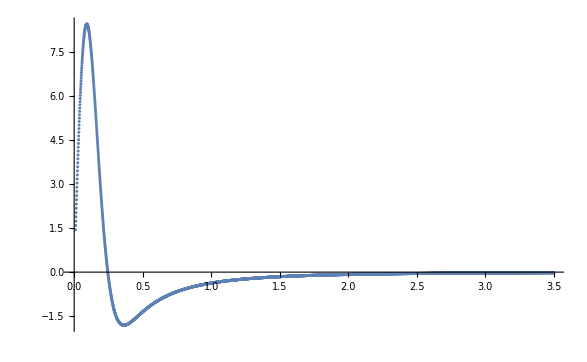

```mathematica
ListPlot[list, PlotRange->Full]
```

```mathematica
a:=FindFit[list,(a1+a2*x+a3*x^2+a4*x^3+a5*x^4)/(1+a6*x+a7*x^2+a8*x^3+a9*x^4),{a1,a2,a3,a4,a5,a6,a7,a8,a9},x]
```

```mathematica
(a1+a2*x+a3*x^2+a4*x^3+a5*x^4)/(1+a6*x+a7*x^2+a8*x^3+a9*x^4)/.{a[[1]],a[[2]],a[[3]],a[[4]],a[[5]],a[[6]],a[[7]],a[[8]],a[[9]]}
```

(0.186637+125.73 x-526.528 x^2+38.9315 x^3+4.19698 x^4)/(1-8.98855 x+119.381 x^2-534.448 x^3+1391.89 x^4)

```mathematica
f[x_]:=(0.1866370227262941+125.72952437538264 x-526.5283847731355 x^2+38.93153523019567 x^3+4.196976666441546 x^4)/(1-8.988550748417875 x+119.3808456858745 x^2-534.4480090380263 x^3+1391.8895523660665 x^4)
```

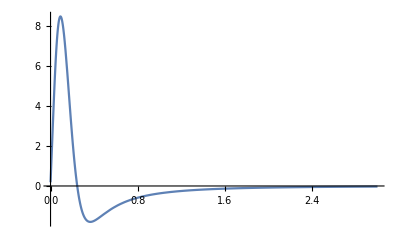

```mathematica
Plot[f[x],{x,0,3},PlotRange->All]
```

```mathematica
NIntegrate[f[x],{x,0,3}]
```

0.228905

```mathematica
listV2:={};
For[i=0.01,i≤ 3.5,i=i+0.001,
AppendTo[listV2,{i,NIntegrate[f[wq],{wq,0,i},Method->"DoubleExponential"]}]]
```

```mathematica
listV2
```

{{0.01,0.00840953},{0.011,0.00998744},{0.012,0.0117019},{0.013,0.0135533},{0.014,0.0155421},{0.015,0.0176683},{0.016,0.0199322},{0.017,0.0223338},{0.018,0.0248732},{0.019,0.0275503},{0.02,0.0303649},{0.021,0.0333167},{0.022,0.0364055},{0.023,0.0396308},{0.024,0.042992},{0.025,0.0464888},{0.026,0.0501203},{0.027,0.0538858},{0.028,0.0577845},{0.029,0.0618156},{0.03,0.065978},{0.031,0.0702707},{0.032,0.0746926},{0.033,0.0792424},{0.034,0.0839189},{0.035,0.0887208},{0.036,0.0936465},{0.037,0.0986947},{0.038,0.103864},{0.039,0.109152},{0.04,0.114558},{0.041,0.12008},{0.042,0.125716},{0.043,0.131464},{0.044,0.137323},{0.045,0.143289},{0.046,0.149363},{0.047,0.15554},{0.048,0.16182},{0.049,0.1682},{0.05,0.174678},{0.051,0.181252},{0.052,0.187919},{0.053,0.194678},{0.054,0.201525},{0.055,0.208459},{0.056,0.215477},{0.057,0.222578},{0.058,0.229757},{0.059,0.237014},{0.06,0.244346},{0.061,0.25175},{0.062,0.259224},{0.063,0.266765},{0.064,0.274371},{0.065,0.282039},{0.066,0.289768},{0.067,0.297554},{0.068,0.305395},{0.069,0.313288},{0.07,0.321232},{0.071,0.329223},{0.072,0.33726},{0.073,0.345339},{0.074,0.353459},{0.075,0.361617},{0.076,0.369811},{0.077,0.378037},{0.078,0.386295},{0.079,0.394581},{0.08,0.402893},{0.081,0.411229},{0.082,0.419586},{0.083,0.427963},{0.084,0.436357},{0.085,0.444765},{0.086,0.453187},{0.087,0.461618},{0.088,0.470058},{0.089,0.478504},{0.09,0.486955},{0.091,0.495407},{0.092,0.503859},{0.093,0.512309},{0.094,0.520756},{0.095,0.529196},{0.096,0.537628},{0.097,0.546051},{0.098,0.554461},{0.099,0.562858},{0.1,0.57124},{0.101,0.579605},{0.102,0.587951},{0.103,0.596276},{0.104,0.604579},{0.105,0.612858},{0.106,0.621111},{0.107,0.629337},{0.108,0.637535},{0.109,0.645702},{0.11,0.653837},{0.111,0.661939},{0.112,0.670006},{0.113,0.678037},{0.114,0.686031},{0.115,0.693985},{0.116,0.7019},{0.117,0.709772},{0.118,0.717602},{0.119,0.725388},{0.12,0.733128},{0.121,0.740822},{0.122,0.748469},{0.123,0.756066},{0.124,0.763614},{0.125,0.771111},{0.126,0.778556},{0.127,0.785948},{0.128,0.793286},{0.129,0.800569},{0.13,0.807796},{0.131,0.814966},{0.132,0.822079},{0.133,0.829133},{0.134,0.836127},{0.135,0.843062},{0.136,0.849936},{0.137,0.856748},{0.138,0.863498},{0.139,0.870185},{0.14,0.876808},{0.141,0.883366},{0.142,0.88986},{0.143,0.896288},{0.144,0.90265},{0.145,0.908945},{0.146,0.915173},{0.147,0.921333},{0.148,0.927426},{0.149,0.933449},{0.15,0.939404},{0.151,0.945289},{0.152,0.951104},{0.153,0.956849},{0.154,0.962523},{0.155,0.968127},{0.156,0.97366},{0.157,0.979121},{0.158,0.98451},{0.159,0.989828},{0.16,0.995074},{0.161,1.00025},{0.162,1.00535},{0.163,1.01038},{0.164,1.01533},{0.165,1.02022},{0.166,1.02503},{0.167,1.02976},{0.168,1.03443},{0.169,1.03902},{0.17,1.04354},{0.171,1.04798},{0.172,1.05236},{0.173,1.05666},{0.174,1.06088},{0.175,1.06504},{0.176,1.06912},{0.177,1.07313},{0.178,1.07707},{0.179,1.08093},{0.18,1.08473},{0.181,1.08845},{0.182,1.0921},{0.183,1.09568},{0.184,1.09918},{0.185,1.10262},{0.186,1.10598},{0.187,1.10928},{0.188,1.11251},{0.189,1.11566},{0.19,1.11875},{0.191,1.12176},{0.192,1.12471},{0.193,1.12759},{0.194,1.1304},{0.195,1.13315},{0.196,1.13583},{0.197,1.13844},{0.198,1.14098},{0.199,1.14346},{0.2,1.14587},{0.201,1.14822},{0.202,1.1505},{0.203,1.15272},{0.204,1.15487},{0.205,1.15696},{0.206,1.15899},{0.207,1.16095},{0.208,1.16286},{0.209,1.1647},{0.21,1.16648},{0.211,1.1682},{0.212,1.16986},{0.213,1.17147},{0.214,1.17301},{0.215,1.1745},{0.216,1.17592},{0.217,1.1773},{0.218,1.17861},{0.219,1.17987},{0.22,1.18107},{0.221,1.18222},{0.222,1.18332},{0.223,1.18436},{0.224,1.18535},{0.225,1.18628},{0.226,1.18716},{0.227,1.188},{0.228,1.18878},{0.229,1.18951},{0.23,1.19019},{0.231,1.19083},{0.232,1.19141},{0.233,1.19195},{0.234,1.19244},{0.235,1.19288},{0.236,1.19328},{0.237,1.19363},{0.238,1.19394},{0.239,1.1942},{0.24,1.19442},{0.241,1.1946},{0.242,1.19474},{0.243,1.19483},{0.244,1.19488},{0.245,1.19489},{0.246,1.19487},{0.247,1.1948},{0.248,1.19469},{0.249,1.19455},{0.25,1.19436},{0.251,1.19414},{0.252,1.19389},{0.253,1.19359},{0.254,1.19327},{0.255,1.1929},{0.256,1.19251},{0.257,1.19208},{0.258,1.19161},{0.259,1.19112},{0.26,1.19059},{0.261,1.19003},{0.262,1.18944},{0.263,1.18882},{0.264,1.18817},{0.265,1.18749},{0.266,1.18678},{0.267,1.18604},{0.268,1.18527},{0.269,1.18448},{0.27,1.18366},{0.271,1.18281},{0.272,1.18194},{0.273,1.18104},{0.274,1.18012},{0.275,1.17917},{0.276,1.1782},{0.277,1.17721},{0.278,1.17619},{0.279,1.17515},{0.28,1.17408},{0.281,1.173},{0.282,1.17189},{0.283,1.17077},{0.284,1.16962},{0.285,1.16846},{0.286,1.16727},{0.287,1.16606},{0.288,1.16484},{0.289,1.1636},{0.29,1.16234},{0.291,1.16106},{0.292,1.15976},{0.293,1.15845},{0.294,1.15713},{0.295,1.15578},{0.296,1.15442},{0.297,1.15305},{0.298,1.15166},{0.299,1.15025},{0.3,1.14884},{0.301,1.1474},{0.302,1.14596},{0.303,1.1445},{0.304,1.14303},{0.305,1.14154},{0.306,1.14005},{0.307,1.13854},{0.308,1.13702},{0.309,1.13549},{0.31,1.13395},{0.311,1.1324},{0.312,1.13083},{0.313,1.12926},{0.314,1.12768},{0.315,1.12609},{0.316,1.12449},{0.317,1.12288},{0.318,1.12126},{0.319,1.11963},{0.32,1.118},{0.321,1.11636},{0.322,1.11471},{0.323,1.11305},{0.324,1.11138},{0.325,1.10971},{0.326,1.10803},{0.327,1.10635},{0.328,1.10466},{0.329,1.10296},{0.33,1.10126},{0.331,1.09955},{0.332,1.09784},{0.333,1.09612},{0.334,1.0944},{0.335,1.09267},{0.336,1.09094},{0.337,1.0892},{0.338,1.08746},{0.339,1.08571},{0.34,1.08396},{0.341,1.08221},{0.342,1.08046},{0.343,1.0787},{0.344,1.07694},{0.345,1.07517},{0.346,1.0734},{0.347,1.07164},{0.348,1.06986},{0.349,1.06809},{0.35,1.06631},{0.351,1.06453},{0.352,1.06275},{0.353,1.06097},{0.354,1.05919},{0.355,1.0574},{0.356,1.05562},{0.357,1.05383},{0.358,1.05204},{0.359,1.05025},{0.36,1.04847},{0.361,1.04668},{0.362,1.04488},{0.363,1.04309},{0.364,1.0413},{0.365,1.03951},{0.366,1.03772},{0.367,1.03593},{0.368,1.03414},{0.369,1.03235},{0.37,1.03056},{0.371,1.02877},{0.372,1.02698},{0.373,1.02519},{0.374,1.02341},{0.375,1.02162},{0.376,1.01983},{0.377,1.01805},{0.378,1.01627},{0.379,1.01448},{0.38,1.0127},{0.381,1.01092},{0.382,1.00915},{0.383,1.00737},{0.384,1.0056},{0.385,1.00382},{0.386,1.00205},{0.387,1.00028},{0.388,0.998516},{0.389,0.996751},{0.39,0.994988},{0.391,0.993227},{0.392,0.991468},{0.393,0.989711},{0.394,0.987957},{0.395,0.986205},{0.396,0.984456},{0.397,0.982709},{0.398,0.980964},{0.399,0.979222},{0.4,0.977483},{0.401,0.975746},{0.402,0.974012},{0.403,0.972281},{0.404,0.970553},{0.405,0.968828},{0.406,0.967105},{0.407,0.965386},{0.408,0.963669},{0.409,0.961955},{0.41,0.960245},{0.411,0.958538},{0.412,0.956833},{0.413,0.955132},{0.414,0.953435},{0.415,0.95174},{0.416,0.950049},{0.417,0.948361},{0.418,0.946676},{0.419,0.944995},{0.42,0.943317},{0.421,0.941643},{0.422,0.939972},{0.423,0.938305},{0.424,0.936641},{0.425,0.934981},{0.426,0.933324},{0.427,0.931671},{0.428,0.930021},{0.429,0.928375},{0.43,0.926733},{0.431,0.925094},{0.432,0.923459},{0.433,0.921828},{0.434,0.920201},{0.435,0.918577},{0.436,0.916957},{0.437,0.915341},{0.438,0.913729},{0.439,0.91212},{0.44,0.910515},{0.441,0.908915},{0.442,0.907318},{0.443,0.905724},{0.444,0.904135},{0.445,0.90255},{0.446,0.900968},{0.447,0.899391},{0.448,0.897817},{0.449,0.896248},{0.45,0.894682},{0.451,0.89312},{0.452,0.891562},{0.453,0.890008},{0.454,0.888459},{0.455,0.886913},{0.456,0.885371},{0.457,0.883833},{0.458,0.882299},{0.459,0.880769},{0.46,0.879243},{0.461,0.877721},{0.462,0.876204},{0.463,0.87469},{0.464,0.87318},{0.465,0.871674},{0.466,0.870172},{0.467,0.868675},{0.468,0.867181},{0.469,0.865691},{0.47,0.864206},{0.471,0.862724},{0.472,0.861247},{0.473,0.859773},{0.474,0.858304},{0.475,0.856838},{0.476,0.855377},{0.477,0.853919},{0.478,0.852466},{0.479,0.851017},{0.48,0.849572},{0.481,0.84813},{0.482,0.846693},{0.483,0.84526},{0.484,0.843831},{0.485,0.842406},{0.486,0.840984},{0.487,0.839567},{0.488,0.838154},{0.489,0.836745},{0.49,0.83534},{0.491,0.833939},{0.492,0.832542},{0.493,0.831149},{0.494,0.829759},{0.495,0.828374},{0.496,0.826993},{0.497,0.825616},{0.498,0.824242},{0.499,0.822873},{0.5,0.821508},{0.501,0.820146},{0.502,0.818789},{0.503,0.817435},{0.504,0.816085},{0.505,0.814739},{0.506,0.813398},{0.507,0.81206},{0.508,0.810726},{0.509,0.809395},{0.51,0.808069},{0.511,0.806747},{0.512,0.805428},{0.513,0.804113},{0.514,0.802802},{0.515,0.801495},{0.516,0.800192},{0.517,0.798893},{0.518,0.797597},{0.519,0.796306},{0.52,0.795018},{0.521,0.793734},{0.522,0.792453},{0.523,0.791177},{0.524,0.789904},{0.525,0.788635},{0.526,0.787369},{0.527,0.786108},{0.528,0.78485},{0.529,0.783596},{0.53,0.782345},{0.531,0.781099},{0.532,0.779856},{0.533,0.778616},{0.534,0.777381},{0.535,0.776149},{0.536,0.77492},{0.537,0.773696},{0.538,0.772474},{0.539,0.771257},{0.54,0.770043},{0.541,0.768833},{0.542,0.767626},{0.543,0.766423},{0.544,0.765224},{0.545,0.764028},{0.546,0.762836},{0.547,0.761647},{0.548,0.760462},{0.549,0.75928},{0.55,0.758102},{0.551,0.756927},{0.552,0.755756},{0.553,0.754588},{0.554,0.753424},{0.555,0.752263},{0.556,0.751106},{0.557,0.749952},{0.558,0.748802},{0.559,0.747655},{0.56,0.746511},{0.561,0.745371},{0.562,0.744234},{0.563,0.743101},{0.564,0.741971},{0.565,0.740844},{0.566,0.739721},{0.567,0.738601},{0.568,0.737485},{0.569,0.736371},{0.57,0.735261},{0.571,0.734155},{0.572,0.733051},{0.573,0.731951},{0.574,0.730854},{0.575,0.729761},{0.576,0.72867},{0.577,0.727583},{0.578,0.7265},{0.579,0.725419},{0.58,0.724342},{0.581,0.723267},{0.582,0.722196},{0.583,0.721128},{0.584,0.720064},{0.585,0.719002},{0.586,0.717944},{0.587,0.716889},{0.588,0.715836},{0.589,0.714787},{0.59,0.713742},{0.591,0.712699},{0.592,0.711659},{0.593,0.710622},{0.594,0.709589},{0.595,0.708558},{0.596,0.707531},{0.597,0.706506},{0.598,0.705485},{0.599,0.704467},{0.6,0.703451},{0.601,0.702439},{0.602,0.701429},{0.603,0.700423},{0.604,0.699419},{0.605,0.698419},{0.606,0.697421},{0.607,0.696426},{0.608,0.695435},{0.609,0.694446},{0.61,0.69346},{0.611,0.692477},{0.612,0.691497},{0.613,0.690519},{0.614,0.689545},{0.615,0.688573},{0.616,0.687605},{0.617,0.686639},{0.618,0.685676},{0.619,0.684715},{0.62,0.683758},{0.621,0.682803},{0.622,0.681851},{0.623,0.680902},{0.624,0.679956},{0.625,0.679012},{0.626,0.678071},{0.627,0.677133},{0.628,0.676198},{0.629,0.675265},{0.63,0.674335},{0.631,0.673408},{0.632,0.672483},{0.633,0.671561},{0.634,0.670642},{0.635,0.669725},{0.636,0.668811},{0.637,0.6679},{0.638,0.666991},{0.639,0.666085},{0.64,0.665182},{0.641,0.664281},{0.642,0.663383},{0.643,0.662487},{0.644,0.661594},{0.645,0.660704},{0.646,0.659816},{0.647,0.65893},{0.648,0.658047},{0.649,0.657167},{0.65,0.656289},{0.651,0.655414},{0.652,0.654541},{0.653,0.653671},{0.654,0.652803},{0.655,0.651937},{0.656,0.651074},{0.657,0.650214},{0.658,0.649356},{0.659,0.6485},{0.66,0.647647},{0.661,0.646797},{0.662,0.645948},{0.663,0.645102},{0.664,0.644259},{0.665,0.643418},{0.666,0.642579},{0.667,0.641743},{0.668,0.640909},{0.669,0.640077},{0.67,0.639248},{0.671,0.638421},{0.672,0.637596},{0.673,0.636774},{0.674,0.635954},{0.675,0.635136},{0.676,0.634321},{0.677,0.633508},{0.678,0.632697},{0.679,0.631888},{0.68,0.631082},{0.681,0.630278},{0.682,0.629476},{0.683,0.628677},{0.684,0.627879},{0.685,0.627084},{0.686,0.626291},{0.687,0.625501},{0.688,0.624712},{0.689,0.623926},{0.69,0.623142},{0.691,0.62236},{0.692,0.62158},{0.693,0.620802},{0.694,0.620027},{0.695,0.619254},{0.696,0.618483},{0.697,0.617714},{0.698,0.616947},{0.699,0.616182},{0.7,0.615419},{0.701,0.614658},{0.702,0.6139},{0.703,0.613143},{0.704,0.612389},{0.705,0.611637},{0.706,0.610887},{0.707,0.610138},{0.708,0.609392},{0.709,0.608648},{0.71,0.607906},{0.711,0.607166},{0.712,0.606428},{0.713,0.605692},{0.714,0.604958},{0.715,0.604226},{0.716,0.603496},{0.717,0.602768},{0.718,0.602042},{0.719,0.601318},{0.72,0.600596},{0.721,0.599875},{0.722,0.599157},{0.723,0.598441},{0.724,0.597727},{0.725,0.597014},{0.726,0.596304},{0.727,0.595595},{0.728,0.594888},{0.729,0.594183},{0.73,0.59348},{0.731,0.592779},{0.732,0.59208},{0.733,0.591383},{0.734,0.590687},{0.735,0.589994},{0.736,0.589302},{0.737,0.588612},{0.738,0.587924},{0.739,0.587238},{0.74,0.586554},{0.741,0.585871},{0.742,0.58519},{0.743,0.584511},{0.744,0.583834},{0.745,0.583159},{0.746,0.582485},{0.747,0.581814},{0.748,0.581144},{0.749,0.580475},{0.75,0.579809},{0.751,0.579144},{0.752,0.578481},{0.753,0.57782},{0.754,0.57716},{0.755,0.576503},{0.756,0.575846},{0.757,0.575192},{0.758,0.57454},{0.759,0.573889},{0.76,0.573239},{0.761,0.572592},{0.762,0.571946},{0.763,0.571302},{0.764,0.570659},{0.765,0.570019},{0.766,0.56938},{0.767,0.568742},{0.768,0.568106},{0.769,0.567472},{0.77,0.56684},{0.771,0.566209},{0.772,0.565579},{0.773,0.564952},{0.774,0.564326},{0.775,0.563701},{0.776,0.563078},{0.777,0.562457},{0.778,0.561838},{0.779,0.56122},{0.78,0.560603},{0.781,0.559988},{0.782,0.559375},{0.783,0.558763},{0.784,0.558153},{0.785,0.557545},{0.786,0.556938},{0.787,0.556332},{0.788,0.555728},{0.789,0.555126},{0.79,0.554525},{0.791,0.553926},{0.792,0.553328},{0.793,0.552731},{0.794,0.552137},{0.795,0.551543},{0.796,0.550952},{0.797,0.550361},{0.798,0.549772},{0.799,0.549185},{0.8,0.548599},{0.801,0.548015},{0.802,0.547432},{0.803,0.546851},{0.804,0.546271},{0.805,0.545692},{0.806,0.545115},{0.807,0.544539},{0.808,0.543965},{0.809,0.543392},{0.81,0.542821},{0.811,0.542251},{0.812,0.541683},{0.813,0.541116},{0.814,0.54055},{0.815,0.539986},{0.816,0.539423},{0.817,0.538861},{0.818,0.538301},{0.819,0.537743},{0.82,0.537185},{0.821,0.536629},{0.822,0.536075},{0.823,0.535522},{0.824,0.53497},{0.825,0.534419},{0.826,0.53387},{0.827,0.533323},{0.828,0.532776},{0.829,0.532231},{0.83,0.531687},{0.831,0.531145},{0.832,0.530604},{0.833,0.530064},{0.834,0.529526},{0.835,0.528989},{0.836,0.528453},{0.837,0.527918},{0.838,0.527385},{0.839,0.526853},{0.84,0.526322},{0.841,0.525793},{0.842,0.525265},{0.843,0.524738},{0.844,0.524213},{0.845,0.523689},{0.846,0.523166},{0.847,0.522644},{0.848,0.522123},{0.849,0.521604},{0.85,0.521086},{0.851,0.52057},{0.852,0.520054},{0.853,0.51954},{0.854,0.519027},{0.855,0.518515},{0.856,0.518005},{0.857,0.517495},{0.858,0.516987},{0.859,0.51648},{0.86,0.515975},{0.861,0.51547},{0.862,0.514967},{0.863,0.514465},{0.864,0.513964},{0.865,0.513464},{0.866,0.512966},{0.867,0.512469},{0.868,0.511972},{0.869,0.511478},{0.87,0.510984},{0.871,0.510491},{0.872,0.51},{0.873,0.509509},{0.874,0.50902},{0.875,0.508532},{0.876,0.508045},{0.877,0.50756},{0.878,0.507075},{0.879,0.506592},{0.88,0.506109},{0.881,0.505628},{0.882,0.505148},{0.883,0.504669},{0.884,0.504191},{0.885,0.503715},{0.886,0.503239},{0.887,0.502764},{0.888,0.502291},{0.889,0.501819},{0.89,0.501348},{0.891,0.500878},{0.892,0.500409},{0.893,0.499941},{0.894,0.499474},{0.895,0.499008},{0.896,0.498543},{0.897,0.49808},{0.898,0.497617},{0.899,0.497156},{0.9,0.496695},{0.901,0.496236},{0.902,0.495778},{0.903,0.49532},{0.904,0.494864},{0.905,0.494409},{0.906,0.493955},{0.907,0.493502},{0.908,0.49305},{0.909,0.492599},{0.91,0.492149},{0.911,0.4917},{0.912,0.491252},{0.913,0.490805},{0.914,0.490359},{0.915,0.489914},{0.916,0.48947},{0.917,0.489027},{0.918,0.488585},{0.919,0.488145},{0.92,0.487705},{0.921,0.487266},{0.922,0.486828},{0.923,0.486391},{0.924,0.485955},{0.925,0.48552},{0.926,0.485086},{0.927,0.484653},{0.928,0.484221},{0.929,0.48379},{0.93,0.48336},{0.931,0.482931},{0.932,0.482503},{0.933,0.482075},{0.934,0.481649},{0.935,0.481224},{0.936,0.4808},{0.937,0.480376},{0.938,0.479954},{0.939,0.479532},{0.94,0.479112},{0.941,0.478692},{0.942,0.478273},{0.943,0.477855},{0.944,0.477438},{0.945,0.477022},{0.946,0.476607},{0.947,0.476193},{0.948,0.47578},{0.949,0.475368},{0.95,0.474956},{0.951,0.474546},{0.952,0.474136},{0.953,0.473728},{0.954,0.47332},{0.955,0.472913},{0.956,0.472507},{0.957,0.472102},{0.958,0.471697},{0.959,0.471294},{0.96,0.470892},{0.961,0.47049},{0.962,0.470089},{0.963,0.469689},{0.964,0.46929},{0.965,0.468892},{0.966,0.468495},{0.967,0.468099},{0.968,0.467703},{0.969,0.467309},{0.97,0.466915},{0.971,0.466522},{0.972,0.46613},{0.973,0.465738},{0.974,0.465348},{0.975,0.464958},{0.976,0.46457},{0.977,0.464182},{0.978,0.463795},{0.979,0.463408},{0.98,0.463023},{0.981,0.462638},{0.982,0.462254},{0.983,0.461871},{0.984,0.461489},{0.985,0.461108},{0.986,0.460728},{0.987,0.460348},{0.988,0.459969},{0.989,0.459591},{0.99,0.459214},{0.991,0.458837},{0.992,0.458461},{0.993,0.458087},{0.994,0.457712},{0.995,0.457339},{0.996,0.456967},{0.997,0.456595},{0.998,0.456224},{0.999,0.455854},{1.,0.455484},{1.001,0.455116},{1.002,0.454748},{1.003,0.454381},{1.004,0.454015},{1.005,0.453649},{1.006,0.453284},{1.007,0.45292},{1.008,0.452557},{1.009,0.452195},{1.01,0.451833},{1.011,0.451472},{1.012,0.451112},{1.013,0.450753},{1.014,0.450394},{1.015,0.450036},{1.016,0.449679},{1.017,0.449322},{1.018,0.448967},{1.019,0.448612},{1.02,0.448257},{1.021,0.447904},{1.022,0.447551},{1.023,0.447199},{1.024,0.446848},{1.025,0.446497},{1.026,0.446147},{1.027,0.445798},{1.028,0.44545},{1.029,0.445102},{1.03,0.444755},{1.031,0.444409},{1.032,0.444063},{1.033,0.443718},{1.034,0.443374},{1.035,0.443031},{1.036,0.442688},{1.037,0.442346},{1.038,0.442004},{1.039,0.441664},{1.04,0.441324},{1.041,0.440985},{1.042,0.440646},{1.043,0.440308},{1.044,0.439971},{1.045,0.439634},{1.046,0.439299},{1.047,0.438963},{1.048,0.438629},{1.049,0.438295},{1.05,0.437962},{1.051,0.43763},{1.052,0.437298},{1.053,0.436967},{1.054,0.436636},{1.055,0.436306},{1.056,0.435977},{1.057,0.435649},{1.058,0.435321},{1.059,0.434994},{1.06,0.434668},{1.061,0.434342},{1.062,0.434017},{1.063,0.433692},{1.064,0.433368},{1.065,0.433045},{1.066,0.432722},{1.067,0.4324},{1.068,0.432079},{1.069,0.431758},{1.07,0.431438},{1.071,0.431119},{1.072,0.4308},{1.073,0.430482},{1.074,0.430165},{1.075,0.429848},{1.076,0.429532},{1.077,0.429216},{1.078,0.428901},{1.079,0.428587},{1.08,0.428273},{1.081,0.42796},{1.082,0.427647},{1.083,0.427335},{1.084,0.427024},{1.085,0.426714},{1.086,0.426403},{1.087,0.426094},{1.088,0.425785},{1.089,0.425477},{1.09,0.425169},{1.091,0.424862},{1.092,0.424556},{1.093,0.42425},{1.094,0.423945},{1.095,0.42364},{1.096,0.423336},{1.097,0.423033},{1.098,0.42273},{1.099,0.422428},{1.1,0.422126},{1.101,0.421825},{1.102,0.421524},{1.103,0.421224},{1.104,0.420925},{1.105,0.420626},{1.106,0.420328},{1.107,0.420031},{1.108,0.419734},{1.109,0.419437},{1.11,0.419141},{1.111,0.418846},{1.112,0.418551},{1.113,0.418257},{1.114,0.417963},{1.115,0.41767},{1.116,0.417378},{1.117,0.417086},{1.118,0.416794},{1.119,0.416504},{1.12,0.416213},{1.121,0.415924},{1.122,0.415634},{1.123,0.415346},{1.124,0.415058},{1.125,0.41477},{1.126,0.414483},{1.127,0.414197},{1.128,0.413911},{1.129,0.413626},{1.13,0.413341},{1.131,0.413057},{1.132,0.412773},{1.133,0.41249},{1.134,0.412207},{1.135,0.411925},{1.136,0.411644},{1.137,0.411363},{1.138,0.411082},{1.139,0.410802},{1.14,0.410523},{1.141,0.410244},{1.142,0.409965},{1.143,0.409687},{1.144,0.40941},{1.145,0.409133},{1.146,0.408857},{1.147,0.408581},{1.148,0.408306},{1.149,0.408031},{1.15,0.407757},{1.151,0.407483},{1.152,0.40721},{1.153,0.406937},{1.154,0.406665},{1.155,0.406393},{1.156,0.406122},{1.157,0.405851},{1.158,0.405581},{1.159,0.405311},{1.16,0.405042},{1.161,0.404774},{1.162,0.404505},{1.163,0.404238},{1.164,0.40397},{1.165,0.403704},{1.166,0.403438},{1.167,0.403172},{1.168,0.402907},{1.169,0.402642},{1.17,0.402378},{1.171,0.402114},{1.172,0.401851},{1.173,0.401588},{1.174,0.401325},{1.175,0.401064},{1.176,0.400802},{1.177,0.400541},{1.178,0.400281},{1.179,0.400021},{1.18,0.399762},{1.181,0.399503},{1.182,0.399244},{1.183,0.398986},{1.184,0.398728},{1.185,0.398471},{1.186,0.398215},{1.187,0.397959},{1.188,0.397703},{1.189,0.397448},{1.19,0.397193},{1.191,0.396939},{1.192,0.396685},{1.193,0.396431},{1.194,0.396178},{1.195,0.395926},{1.196,0.395674},{1.197,0.395422},{1.198,0.395171},{1.199,0.394921},{1.2,0.39467},{1.201,0.394421},{1.202,0.394171},{1.203,0.393922},{1.204,0.393674},{1.205,0.393426},{1.206,0.393179},{1.207,0.392931},{1.208,0.392685},{1.209,0.392439},{1.21,0.392193},{1.211,0.391948},{1.212,0.391703},{1.213,0.391458},{1.214,0.391214},{1.215,0.390971},{1.216,0.390728},{1.217,0.390485},{1.218,0.390243},{1.219,0.390001},{1.22,0.389759},{1.221,0.389518},{1.222,0.389278},{1.223,0.389038},{1.224,0.388798},{1.225,0.388559},{1.226,0.38832},{1.227,0.388081},{1.228,0.387843},{1.229,0.387606},{1.23,0.387369},{1.231,0.387132},{1.232,0.386895},{1.233,0.386659},{1.234,0.386424},{1.235,0.386189},{1.236,0.385954},{1.237,0.38572},{1.238,0.385486},{1.239,0.385253},{1.24,0.38502},{1.241,0.384787},{1.242,0.384555},{1.243,0.384323},{1.244,0.384091},{1.245,0.38386},{1.246,0.38363},{1.247,0.383399},{1.248,0.38317},{1.249,0.38294},{1.25,0.382711},{1.251,0.382483},{1.252,0.382254},{1.253,0.382027},{1.254,0.381799},{1.255,0.381572},{1.256,0.381345},{1.257,0.381119},{1.258,0.380893},{1.259,0.380668},{1.26,0.380443},{1.261,0.380218},{1.262,0.379994},{1.263,0.37977},{1.264,0.379546},{1.265,0.379323},{1.266,0.3791},{1.267,0.378878},{1.268,0.378656},{1.269,0.378434},{1.27,0.378213},{1.271,0.377992},{1.272,0.377772},{1.273,0.377551},{1.274,0.377332},{1.275,0.377112},{1.276,0.376893},{1.277,0.376675},{1.278,0.376456},{1.279,0.376239},{1.28,0.376021},{1.281,0.375804},{1.282,0.375587},{1.283,0.375371},{1.284,0.375155},{1.285,0.374939},{1.286,0.374724},{1.287,0.374509},{1.288,0.374294},{1.289,0.37408},{1.29,0.373866},{1.291,0.373653},{1.292,0.37344},{1.293,0.373227},{1.294,0.373014},{1.295,0.372802},{1.296,0.372591},{1.297,0.372379},{1.298,0.372168},{1.299,0.371958},{1.3,0.371747},{1.301,0.371538},{1.302,0.371328},{1.303,0.371119},{1.304,0.37091},{1.305,0.370701},{1.306,0.370493},{1.307,0.370285},{1.308,0.370078},{1.309,0.369871},{1.31,0.369664},{1.311,0.369457},{1.312,0.369251},{1.313,0.369046},{1.314,0.36884},{1.315,0.368635},{1.316,0.36843},{1.317,0.368226},{1.318,0.368022},{1.319,0.367818},{1.32,0.367615},{1.321,0.367412},{1.322,0.367209},{1.323,0.367007},{1.324,0.366805},{1.325,0.366603},{1.326,0.366402},{1.327,0.366201},{1.328,0.366},{1.329,0.365799},{1.33,0.365599},{1.331,0.3654},{1.332,0.3652},{1.333,0.365001},{1.334,0.364802},{1.335,0.364604},{1.336,0.364406},{1.337,0.364208},{1.338,0.364011},{1.339,0.363814},{1.34,0.363617},{1.341,0.36342},{1.342,0.363224},{1.343,0.363028},{1.344,0.362833},{1.345,0.362638},{1.346,0.362443},{1.347,0.362248},{1.348,0.362054},{1.349,0.36186},{1.35,0.361666},{1.351,0.361473},{1.352,0.36128},{1.353,0.361087},{1.354,0.360895},{1.355,0.360703},{1.356,0.360511},{1.357,0.36032},{1.358,0.360129},{1.359,0.359938},{1.36,0.359747},{1.361,0.359557},{1.362,0.359367},{1.363,0.359178},{1.364,0.358988},{1.365,0.358799},{1.366,0.358611},{1.367,0.358422},{1.368,0.358234},{1.369,0.358047},{1.37,0.357859},{1.371,0.357672},{1.372,0.357485},{1.373,0.357298},{1.374,0.357112},{1.375,0.356926},{1.376,0.356741},{1.377,0.356555},{1.378,0.35637},{1.379,0.356185},{1.38,0.356001},{1.381,0.355817},{1.382,0.355633},{1.383,0.355449},{1.384,0.355266},{1.385,0.355083},{1.386,0.3549},{1.387,0.354717},{1.388,0.354535},{1.389,0.354353},{1.39,0.354172},{1.391,0.35399},{1.392,0.353809},{1.393,0.353629},{1.394,0.353448},{1.395,0.353268},{1.396,0.353088},{1.397,0.352909},{1.398,0.352729},{1.399,0.35255},{1.4,0.352372},{1.401,0.352193},{1.402,0.352015},{1.403,0.351837},{1.404,0.351659},{1.405,0.351482},{1.406,0.351305},{1.407,0.351128},{1.408,0.350952},{1.409,0.350775},{1.41,0.350599},{1.411,0.350424},{1.412,0.350248},{1.413,0.350073},{1.414,0.349898},{1.415,0.349724},{1.416,0.349549},{1.417,0.349375},{1.418,0.349201},{1.419,0.349028},{1.42,0.348855},{1.421,0.348682},{1.422,0.348509},{1.423,0.348336},{1.424,0.348164},{1.425,0.347992},{1.426,0.347821},{1.427,0.347649},{1.428,0.347478},{1.429,0.347307},{1.43,0.347137},{1.431,0.346966},{1.432,0.346796},{1.433,0.346627},{1.434,0.346457},{1.435,0.346288},{1.436,0.346119},{1.437,0.34595},{1.438,0.345781},{1.439,0.345613},{1.44,0.345445},{1.441,0.345278},{1.442,0.34511},{1.443,0.344943},{1.444,0.344776},{1.445,0.344609},{1.446,0.344443},{1.447,0.344277},{1.448,0.344111},{1.449,0.343945},{1.45,0.343779},{1.451,0.343614},{1.452,0.343449},{1.453,0.343285},{1.454,0.34312},{1.455,0.342956},{1.456,0.342792},{1.457,0.342628},{1.458,0.342465},{1.459,0.342302},{1.46,0.342139},{1.461,0.341976},{1.462,0.341814},{1.463,0.341652},{1.464,0.34149},{1.465,0.341328},{1.466,0.341166},{1.467,0.341005},{1.468,0.340844},{1.469,0.340683},{1.47,0.340523},{1.471,0.340363},{1.472,0.340203},{1.473,0.340043},{1.474,0.339883},{1.475,0.339724},{1.476,0.339565},{1.477,0.339406},{1.478,0.339248},{1.479,0.339089},{1.48,0.338931},{1.481,0.338773},{1.482,0.338616},{1.483,0.338458},{1.484,0.338301},{1.485,0.338144},{1.486,0.337987},{1.487,0.337831},{1.488,0.337675},{1.489,0.337519},{1.49,0.337363},{1.491,0.337207},{1.492,0.337052},{1.493,0.336897},{1.494,0.336742},{1.495,0.336588},{1.496,0.336433},{1.497,0.336279},{1.498,0.336125},{1.499,0.335972},{1.5,0.335818},{1.501,0.335665},{1.502,0.335512},{1.503,0.335359},{1.504,0.335206},{1.505,0.335054},{1.506,0.334902},{1.507,0.33475},{1.508,0.334598},{1.509,0.334447},{1.51,0.334296},{1.511,0.334145},{1.512,0.333994},{1.513,0.333843},{1.514,0.333693},{1.515,0.333543},{1.516,0.333393},{1.517,0.333243},{1.518,0.333094},{1.519,0.332945},{1.52,0.332796},{1.521,0.332647},{1.522,0.332498},{1.523,0.33235},{1.524,0.332202},{1.525,0.332054},{1.526,0.331906},{1.527,0.331759},{1.528,0.331611},{1.529,0.331464},{1.53,0.331317},{1.531,0.331171},{1.532,0.331024},{1.533,0.330878},{1.534,0.330732},{1.535,0.330586},{1.536,0.330441},{1.537,0.330295},{1.538,0.33015},{1.539,0.330005},{1.54,0.32986},{1.541,0.329716},{1.542,0.329572},{1.543,0.329428},{1.544,0.329284},{1.545,0.32914},{1.546,0.328996},{1.547,0.328853},{1.548,0.32871},{1.549,0.328567},{1.55,0.328424},{1.551,0.328282},{1.552,0.32814},{1.553,0.327998},{1.554,0.327856},{1.555,0.327714},{1.556,0.327573},{1.557,0.327431},{1.558,0.32729},{1.559,0.32715},{1.56,0.327009},{1.561,0.326868},{1.562,0.326728},{1.563,0.326588},{1.564,0.326448},{1.565,0.326309},{1.566,0.326169},{1.567,0.32603},{1.568,0.325891},{1.569,0.325752},{1.57,0.325613},{1.571,0.325475},{1.572,0.325337},{1.573,0.325199},{1.574,0.325061},{1.575,0.324923},{1.576,0.324786},{1.577,0.324648},{1.578,0.324511},{1.579,0.324374},{1.58,0.324238},{1.581,0.324101},{1.582,0.323965},{1.583,0.323829},{1.584,0.323693},{1.585,0.323557},{1.586,0.323422},{1.587,0.323286},{1.588,0.323151},{1.589,0.323016},{1.59,0.322881},{1.591,0.322747},{1.592,0.322612},{1.593,0.322478},{1.594,0.322344},{1.595,0.32221},{1.596,0.322077},{1.597,0.321943},{1.598,0.32181},{1.599,0.321677},{1.6,0.321544},{1.601,0.321411},{1.602,0.321279},{1.603,0.321146},{1.604,0.321014},{1.605,0.320882},{1.606,0.32075},{1.607,0.320619},{1.608,0.320487},{1.609,0.320356},{1.61,0.320225},{1.611,0.320094},{1.612,0.319963},{1.613,0.319833},{1.614,0.319702},{1.615,0.319572},{1.616,0.319442},{1.617,0.319313},{1.618,0.319183},{1.619,0.319053},{1.62,0.318924},{1.621,0.318795},{1.622,0.318666},{1.623,0.318537},{1.624,0.318409},{1.625,0.318281},{1.626,0.318152},{1.627,0.318024},{1.628,0.317897},{1.629,0.317769},{1.63,0.317641},{1.631,0.317514},{1.632,0.317387},{1.633,0.31726},{1.634,0.317133},{1.635,0.317007},{1.636,0.31688},{1.637,0.316754},{1.638,0.316628},{1.639,0.316502},{1.64,0.316376},{1.641,0.31625},{1.642,0.316125},{1.643,0.316},{1.644,0.315875},{1.645,0.31575},{1.646,0.315625},{1.647,0.315501},{1.648,0.315376},{1.649,0.315252},{1.65,0.315128},{1.651,0.315004},{1.652,0.31488},{1.653,0.314757},{1.654,0.314633},{1.655,0.31451},{1.656,0.314387},{1.657,0.314264},{1.658,0.314142},{1.659,0.314019},{1.66,0.313897},{1.661,0.313775},{1.662,0.313652},{1.663,0.313531},{1.664,0.313409},{1.665,0.313287},{1.666,0.313166},{1.667,0.313045},{1.668,0.312924},{1.669,0.312803},{1.67,0.312682},{1.671,0.312561},{1.672,0.312441},{1.673,0.312321},{1.674,0.312201},{1.675,0.312081},{1.676,0.311961},{1.677,0.311841},{1.678,0.311722},{1.679,0.311603},{1.68,0.311484},{1.681,0.311365},{1.682,0.311246},{1.683,0.311127},{1.684,0.311009},{1.685,0.31089},{1.686,0.310772},{1.687,0.310654},{1.688,0.310536},{1.689,0.310419},{1.69,0.310301},{1.691,0.310184},{1.692,0.310067},{1.693,0.30995},{1.694,0.309833},{1.695,0.309716},{1.696,0.309599},{1.697,0.309483},{1.698,0.309367},{1.699,0.30925},{1.7,0.309134},{1.701,0.309019},{1.702,0.308903},{1.703,0.308787},{1.704,0.308672},{1.705,0.308557},{1.706,0.308442},{1.707,0.308327},{1.708,0.308212},{1.709,0.308097},{1.71,0.307983},{1.711,0.307869},{1.712,0.307755},{1.713,0.307641},{1.714,0.307527},{1.715,0.307413},{1.716,0.307299},{1.717,0.307186},{1.718,0.307073},{1.719,0.30696},{1.72,0.306847},{1.721,0.306734},{1.722,0.306621},{1.723,0.306509},{1.724,0.306396},{1.725,0.306284},{1.726,0.306172},{1.727,0.30606},{1.728,0.305948},{1.729,0.305837},{1.73,0.305725},{1.731,0.305614},{1.732,0.305503},{1.733,0.305392},{1.734,0.305281},{1.735,0.30517},{1.736,0.305059},{1.737,0.304949},{1.738,0.304839},{1.739,0.304728},{1.74,0.304618},{1.741,0.304508},{1.742,0.304399},{1.743,0.304289},{1.744,0.30418},{1.745,0.30407},{1.746,0.303961},{1.747,0.303852},{1.748,0.303743},{1.749,0.303634},{1.75,0.303526},{1.751,0.303417},{1.752,0.303309},{1.753,0.303201},{1.754,0.303093},{1.755,0.302985},{1.756,0.302877},{1.757,0.302769},{1.758,0.302662},{1.759,0.302554},{1.76,0.302447},{1.761,0.30234},{1.762,0.302233},{1.763,0.302126},{1.764,0.30202},{1.765,0.301913},{1.766,0.301807},{1.767,0.3017},{1.768,0.301594},{1.769,0.301488},{1.77,0.301382},{1.771,0.301277},{1.772,0.301171},{1.773,0.301066},{1.774,0.30096},{1.775,0.300855},{1.776,0.30075},{1.777,0.300645},{1.778,0.30054},{1.779,0.300436},{1.78,0.300331},{1.781,0.300227},{1.782,0.300123},{1.783,0.300018},{1.784,0.299914},{1.785,0.299811},{1.786,0.299707},{1.787,0.299603},{1.788,0.2995},{1.789,0.299396},{1.79,0.299293},{1.791,0.29919},{1.792,0.299087},{1.793,0.298984},{1.794,0.298882},{1.795,0.298779},{1.796,0.298677},{1.797,0.298575},{1.798,0.298472},{1.799,0.29837},{1.8,0.298269},{1.801,0.298167},{1.802,0.298065},{1.803,0.297964},{1.804,0.297862},{1.805,0.297761},{1.806,0.29766},{1.807,0.297559},{1.808,0.297458},{1.809,0.297357},{1.81,0.297257},{1.811,0.297156},{1.812,0.297056},{1.813,0.296956},{1.814,0.296855},{1.815,0.296755},{1.816,0.296656},{1.817,0.296556},{1.818,0.296456},{1.819,0.296357},{1.82,0.296257},{1.821,0.296158},{1.822,0.296059},{1.823,0.29596},{1.824,0.295861},{1.825,0.295762},{1.826,0.295664},{1.827,0.295565},{1.828,0.295467},{1.829,0.295369},{1.83,0.295271},{1.831,0.295173},{1.832,0.295075},{1.833,0.294977},{1.834,0.294879},{1.835,0.294782},{1.836,0.294684},{1.837,0.294587},{1.838,0.29449},{1.839,0.294393},{1.84,0.294296},{1.841,0.294199},{1.842,0.294102},{1.843,0.294006},{1.844,0.293909},{1.845,0.293813},{1.846,0.293717},{1.847,0.293621},{1.848,0.293525},{1.849,0.293429},{1.85,0.293333},{1.851,0.293238},{1.852,0.293142},{1.853,0.293047},{1.854,0.292952},{1.855,0.292856},{1.856,0.292761},{1.857,0.292667},{1.858,0.292572},{1.859,0.292477},{1.86,0.292383},{1.861,0.292288},{1.862,0.292194},{1.863,0.2921},{1.864,0.292005},{1.865,0.291911},{1.866,0.291818},{1.867,0.291724},{1.868,0.29163},{1.869,0.291537},{1.87,0.291443},{1.871,0.29135},{1.872,0.291257},{1.873,0.291164},{1.874,0.291071},{1.875,0.290978},{1.876,0.290885},{1.877,0.290793},{1.878,0.2907},{1.879,0.290608},{1.88,0.290516},{1.881,0.290423},{1.882,0.290331},{1.883,0.290239},{1.884,0.290148},{1.885,0.290056},{1.886,0.289964},{1.887,0.289873},{1.888,0.289781},{1.889,0.28969},{1.89,0.289599},{1.891,0.289508},{1.892,0.289417},{1.893,0.289326},{1.894,0.289236},{1.895,0.289145},{1.896,0.289054},{1.897,0.288964},{1.898,0.288874},{1.899,0.288784},{1.9,0.288694},{1.901,0.288604},{1.902,0.288514},{1.903,0.288424},{1.904,0.288334},{1.905,0.288245},{1.906,0.288156},{1.907,0.288066},{1.908,0.287977},{1.909,0.287888},{1.91,0.287799},{1.911,0.28771},{1.912,0.287621},{1.913,0.287533},{1.914,0.287444},{1.915,0.287356},{1.916,0.287267},{1.917,0.287179},{1.918,0.287091},{1.919,0.287003},{1.92,0.286915},{1.921,0.286827},{1.922,0.28674},{1.923,0.286652},{1.924,0.286564},{1.925,0.286477},{1.926,0.28639},{1.927,0.286303},{1.928,0.286216},{1.929,0.286129},{1.93,0.286042},{1.931,0.285955},{1.932,0.285868},{1.933,0.285782},{1.934,0.285695},{1.935,0.285609},{1.936,0.285523},{1.937,0.285436},{1.938,0.28535},{1.939,0.285264},{1.94,0.285179},{1.941,0.285093},{1.942,0.285007},{1.943,0.284922},{1.944,0.284836},{1.945,0.284751},{1.946,0.284666},{1.947,0.284581},{1.948,0.284495},{1.949,0.284411},{1.95,0.284326},{1.951,0.284241},{1.952,0.284156},{1.953,0.284072},{1.954,0.283987},{1.955,0.283903},{1.956,0.283819},{1.957,0.283735},{1.958,0.283651},{1.959,0.283567},{1.96,0.283483},{1.961,0.283399},{1.962,0.283315},{1.963,0.283232},{1.964,0.283148},{1.965,0.283065},{1.966,0.282982},{1.967,0.282899},{1.968,0.282816},{1.969,0.282733},{1.97,0.28265},{1.971,0.282567},{1.972,0.282484},{1.973,0.282402},{1.974,0.282319},{1.975,0.282237},{1.976,0.282155},{1.977,0.282073},{1.978,0.28199},{1.979,0.281908},{1.98,0.281827},{1.981,0.281745},{1.982,0.281663},{1.983,0.281581},{1.984,0.2815},{1.985,0.281419},{1.986,0.281337},{1.987,0.281256},{1.988,0.281175},{1.989,0.281094},{1.99,0.281013},{1.991,0.280932},{1.992,0.280851},{1.993,0.280771},{1.994,0.28069},{1.995,0.280609},{1.996,0.280529},{1.997,0.280449},{1.998,0.280369},{1.999,0.280288},{2.,0.280208},{2.001,0.280129},{2.002,0.280049},{2.003,0.279969},{2.004,0.279889},{2.005,0.27981},{2.006,0.27973},{2.007,0.279651},{2.008,0.279572},{2.009,0.279492},{2.01,0.279413},{2.011,0.279334},{2.012,0.279255},{2.013,0.279177},{2.014,0.279098},{2.015,0.279019},{2.016,0.278941},{2.017,0.278862},{2.018,0.278784},{2.019,0.278706},{2.02,0.278627},{2.021,0.278549},{2.022,0.278471},{2.023,0.278393},{2.024,0.278315},{2.025,0.278238},{2.026,0.27816},{2.027,0.278083},{2.028,0.278005},{2.029,0.277928},{2.03,0.27785},{2.031,0.277773},{2.032,0.277696},{2.033,0.277619},{2.034,0.277542},{2.035,0.277465},{2.036,0.277388},{2.037,0.277312},{2.038,0.277235},{2.039,0.277159},{2.04,0.277082},{2.041,0.277006},{2.042,0.27693},{2.043,0.276853},{2.044,0.276777},{2.045,0.276701},{2.046,0.276625},{2.047,0.27655},{2.048,0.276474},{2.049,0.276398},{2.05,0.276323},{2.051,0.276247},{2.052,0.276172},{2.053,0.276096},{2.054,0.276021},{2.055,0.275946},{2.056,0.275871},{2.057,0.275796},{2.058,0.275721},{2.059,0.275646},{2.06,0.275572},{2.061,0.275497},{2.062,0.275423},{2.063,0.275348},{2.064,0.275274},{2.065,0.275199},{2.066,0.275125},{2.067,0.275051},{2.068,0.274977},{2.069,0.274903},{2.07,0.274829},{2.071,0.274755},{2.072,0.274682},{2.073,0.274608},{2.074,0.274535},{2.075,0.274461},{2.076,0.274388},{2.077,0.274314},{2.078,0.274241},{2.079,0.274168},{2.08,0.274095},{2.081,0.274022},{2.082,0.273949},{2.083,0.273876},{2.084,0.273804},{2.085,0.273731},{2.086,0.273658},{2.087,0.273586},{2.088,0.273514},{2.089,0.273441},{2.09,0.273369},{2.091,0.273297},{2.092,0.273225},{2.093,0.273153},{2.094,0.273081},{2.095,0.273009},{2.096,0.272937},{2.097,0.272866},{2.098,0.272794},{2.099,0.272723},{2.1,0.272651},{2.101,0.27258},{2.102,0.272508},{2.103,0.272437},{2.104,0.272366},{2.105,0.272295},{2.106,0.272224},{2.107,0.272153},{2.108,0.272082},{2.109,0.272012},{2.11,0.271941},{2.111,0.27187},{2.112,0.2718},{2.113,0.27173},{2.114,0.271659},{2.115,0.271589},{2.116,0.271519},{2.117,0.271449},{2.118,0.271379},{2.119,0.271309},{2.12,0.271239},{2.121,0.271169},{2.122,0.271099},{2.123,0.27103},{2.124,0.27096},{2.125,0.270891},{2.126,0.270821},{2.127,0.270752},{2.128,0.270683},{2.129,0.270613},{2.13,0.270544},{2.131,0.270475},{2.132,0.270406},{2.133,0.270338},{2.134,0.270269},{2.135,0.2702},{2.136,0.270131},{2.137,0.270063},{2.138,0.269994},{2.139,0.269926},{2.14,0.269857},{2.141,0.269789},{2.142,0.269721},{2.143,0.269653},{2.144,0.269585},{2.145,0.269517},{2.146,0.269449},{2.147,0.269381},{2.148,0.269313},{2.149,0.269246},{2.15,0.269178},{2.151,0.269111},{2.152,0.269043},{2.153,0.268976},{2.154,0.268908},{2.155,0.268841},{2.156,0.268774},{2.157,0.268707},{2.158,0.26864},{2.159,0.268573},{2.16,0.268506},{2.161,0.268439},{2.162,0.268373},{2.163,0.268306},{2.164,0.268239},{2.165,0.268173},{2.166,0.268106},{2.167,0.26804},{2.168,0.267974},{2.169,0.267907},{2.17,0.267841},{2.171,0.267775},{2.172,0.267709},{2.173,0.267643},{2.174,0.267577},{2.175,0.267512},{2.176,0.267446},{2.177,0.26738},{2.178,0.267315},{2.179,0.267249},{2.18,0.267184},{2.181,0.267118},{2.182,0.267053},{2.183,0.266988},{2.184,0.266923},{2.185,0.266858},{2.186,0.266792},{2.187,0.266728},{2.188,0.266663},{2.189,0.266598},{2.19,0.266533},{2.191,0.266468},{2.192,0.266404},{2.193,0.266339},{2.194,0.266275},{2.195,0.26621},{2.196,0.266146},{2.197,0.266082},{2.198,0.266018},{2.199,0.265954},{2.2,0.26589},{2.201,0.265826},{2.202,0.265762},{2.203,0.265698},{2.204,0.265634},{2.205,0.26557},{2.206,0.265507},{2.207,0.265443},{2.208,0.26538},{2.209,0.265316},{2.21,0.265253},{2.211,0.265189},{2.212,0.265126},{2.213,0.265063},{2.214,0.265},{2.215,0.264937},{2.216,0.264874},{2.217,0.264811},{2.218,0.264748},{2.219,0.264686},{2.22,0.264623},{2.221,0.26456},{2.222,0.264498},{2.223,0.264435},{2.224,0.264373},{2.225,0.26431},{2.226,0.264248},{2.227,0.264186},{2.228,0.264124},{2.229,0.264062},{2.23,0.264},{2.231,0.263938},{2.232,0.263876},{2.233,0.263814},{2.234,0.263752},{2.235,0.26369},{2.236,0.263629},{2.237,0.263567},{2.238,0.263506},{2.239,0.263444},{2.24,0.263383},{2.241,0.263321},{2.242,0.26326},{2.243,0.263199},{2.244,0.263138},{2.245,0.263077},{2.246,0.263016},{2.247,0.262955},{2.248,0.262894},{2.249,0.262833},{2.25,0.262773},{2.251,0.262712},{2.252,0.262651},{2.253,0.262591},{2.254,0.26253},{2.255,0.26247},{2.256,0.262409},{2.257,0.262349},{2.258,0.262289},{2.259,0.262229},{2.26,0.262169},{2.261,0.262109},{2.262,0.262049},{2.263,0.261989},{2.264,0.261929},{2.265,0.261869},{2.266,0.261809},{2.267,0.26175},{2.268,0.26169},{2.269,0.261631},{2.27,0.261571},{2.271,0.261512},{2.272,0.261452},{2.273,0.261393},{2.274,0.261334},{2.275,0.261275},{2.276,0.261216},{2.277,0.261157},{2.278,0.261098},{2.279,0.261039},{2.28,0.26098},{2.281,0.260921},{2.282,0.260862},{2.283,0.260804},{2.284,0.260745},{2.285,0.260686},{2.286,0.260628},{2.287,0.260569},{2.288,0.260511},{2.289,0.260453},{2.29,0.260395},{2.291,0.260336},{2.292,0.260278},{2.293,0.26022},{2.294,0.260162},{2.295,0.260104},{2.296,0.260046},{2.297,0.259988},{2.298,0.259931},{2.299,0.259873},{2.3,0.259815},{2.301,0.259758},{2.302,0.2597},{2.303,0.259643},{2.304,0.259585},{2.305,0.259528},{2.306,0.259471},{2.307,0.259413},{2.308,0.259356},{2.309,0.259299},{2.31,0.259242},{2.311,0.259185},{2.312,0.259128},{2.313,0.259071},{2.314,0.259015},{2.315,0.258958},{2.316,0.258901},{2.317,0.258844},{2.318,0.258788},{2.319,0.258731},{2.32,0.258675},{2.321,0.258618},{2.322,0.258562},{2.323,0.258506},{2.324,0.25845},{2.325,0.258393},{2.326,0.258337},{2.327,0.258281},{2.328,0.258225},{2.329,0.258169},{2.33,0.258113},{2.331,0.258057},{2.332,0.258002},{2.333,0.257946},{2.334,0.25789},{2.335,0.257835},{2.336,0.257779},{2.337,0.257724},{2.338,0.257668},{2.339,0.257613},{2.34,0.257557},{2.341,0.257502},{2.342,0.257447},{2.343,0.257392},{2.344,0.257337},{2.345,0.257282},{2.346,0.257227},{2.347,0.257172},{2.348,0.257117},{2.349,0.257062},{2.35,0.257007},{2.351,0.256953},{2.352,0.256898},{2.353,0.256843},{2.354,0.256789},{2.355,0.256734},{2.356,0.25668},{2.357,0.256626},{2.358,0.256571},{2.359,0.256517},{2.36,0.256463},{2.361,0.256409},{2.362,0.256355},{2.363,0.2563},{2.364,0.256246},{2.365,0.256193},{2.366,0.256139},{2.367,0.256085},{2.368,0.256031},{2.369,0.255977},{2.37,0.255924},{2.371,0.25587},{2.372,0.255817},{2.373,0.255763},{2.374,0.25571},{2.375,0.255656},{2.376,0.255603},{2.377,0.25555},{2.378,0.255496},{2.379,0.255443},{2.38,0.25539},{2.381,0.255337},{2.382,0.255284},{2.383,0.255231},{2.384,0.255178},{2.385,0.255125},{2.386,0.255072},{2.387,0.25502},{2.388,0.254967},{2.389,0.254914},{2.39,0.254862},{2.391,0.254809},{2.392,0.254757},{2.393,0.254704},{2.394,0.254652},{2.395,0.2546},{2.396,0.254547},{2.397,0.254495},{2.398,0.254443},{2.399,0.254391},{2.4,0.254339},{2.401,0.254287},{2.402,0.254235},{2.403,0.254183},{2.404,0.254131},{2.405,0.254079},{2.406,0.254027},{2.407,0.253976},{2.408,0.253924},{2.409,0.253872},{2.41,0.253821},{2.411,0.253769},{2.412,0.253718},{2.413,0.253667},{2.414,0.253615},{2.415,0.253564},{2.416,0.253513},{2.417,0.253461},{2.418,0.25341},{2.419,0.253359},{2.42,0.253308},{2.421,0.253257},{2.422,0.253206},{2.423,0.253155},{2.424,0.253105},{2.425,0.253054},{2.426,0.253003},{2.427,0.252952},{2.428,0.252902},{2.429,0.252851},{2.43,0.252801},{2.431,0.25275},{2.432,0.2527},{2.433,0.252649},{2.434,0.252599},{2.435,0.252549},{2.436,0.252498},{2.437,0.252448},{2.438,0.252398},{2.439,0.252348},{2.44,0.252298},{2.441,0.252248},{2.442,0.252198},{2.443,0.252148},{2.444,0.252098},{2.445,0.252049},{2.446,0.251999},{2.447,0.251949},{2.448,0.2519},{2.449,0.25185},{2.45,0.2518},{2.451,0.251751},{2.452,0.251702},{2.453,0.251652},{2.454,0.251603},{2.455,0.251553},{2.456,0.251504},{2.457,0.251455},{2.458,0.251406},{2.459,0.251357},{2.46,0.251308},{2.461,0.251259},{2.462,0.25121},{2.463,0.251161},{2.464,0.251112},{2.465,0.251063},{2.466,0.251014},{2.467,0.250966},{2.468,0.250917},{2.469,0.250868},{2.47,0.25082},{2.471,0.250771},{2.472,0.250723},{2.473,0.250674},{2.474,0.250626},{2.475,0.250578},{2.476,0.250529},{2.477,0.250481},{2.478,0.250433},{2.479,0.250385},{2.48,0.250337},{2.481,0.250289},{2.482,0.250241},{2.483,0.250193},{2.484,0.250145},{2.485,0.250097},{2.486,0.250049},{2.487,0.250001},{2.488,0.249954},{2.489,0.249906},{2.49,0.249858},{2.491,0.249811},{2.492,0.249763},{2.493,0.249716},{2.494,0.249668},{2.495,0.249621},{2.496,0.249573},{2.497,0.249526},{2.498,0.249479},{2.499,0.249432},{2.5,0.249384},{2.501,0.249337},{2.502,0.24929},{2.503,0.249243},{2.504,0.249196},{2.505,0.249149},{2.506,0.249102},{2.507,0.249055},{2.508,0.249009},{2.509,0.248962},{2.51,0.248915},{2.511,0.248868},{2.512,0.248822},{2.513,0.248775},{2.514,0.248729},{2.515,0.248682},{2.516,0.248636},{2.517,0.248589},{2.518,0.248543},{2.519,0.248497},{2.52,0.24845},{2.521,0.248404},{2.522,0.248358},{2.523,0.248312},{2.524,0.248266},{2.525,0.24822},{2.526,0.248174},{2.527,0.248128},{2.528,0.248082},{2.529,0.248036},{2.53,0.24799},{2.531,0.247944},{2.532,0.247899},{2.533,0.247853},{2.534,0.247807},{2.535,0.247762},{2.536,0.247716},{2.537,0.247671},{2.538,0.247625},{2.539,0.24758},{2.54,0.247534},{2.541,0.247489},{2.542,0.247444},{2.543,0.247399},{2.544,0.247353},{2.545,0.247308},{2.546,0.247263},{2.547,0.247218},{2.548,0.247173},{2.549,0.247128},{2.55,0.247083},{2.551,0.247038},{2.552,0.246993},{2.553,0.246948},{2.554,0.246904},{2.555,0.246859},{2.556,0.246814},{2.557,0.24677},{2.558,0.246725},{2.559,0.24668},{2.56,0.246636},{2.561,0.246591},{2.562,0.246547},{2.563,0.246502},{2.564,0.246458},{2.565,0.246414},{2.566,0.24637},{2.567,0.246325},{2.568,0.246281},{2.569,0.246237},{2.57,0.246193},{2.571,0.246149},{2.572,0.246105},{2.573,0.246061},{2.574,0.246017},{2.575,0.245973},{2.576,0.245929},{2.577,0.245885},{2.578,0.245842},{2.579,0.245798},{2.58,0.245754},{2.581,0.245711},{2.582,0.245667},{2.583,0.245623},{2.584,0.24558},{2.585,0.245536},{2.586,0.245493},{2.587,0.24545},{2.588,0.245406},{2.589,0.245363},{2.59,0.24532},{2.591,0.245276},{2.592,0.245233},{2.593,0.24519},{2.594,0.245147},{2.595,0.245104},{2.596,0.245061},{2.597,0.245018},{2.598,0.244975},{2.599,0.244932},{2.6,0.244889},{2.601,0.244846},{2.602,0.244804},{2.603,0.244761},{2.604,0.244718},{2.605,0.244675},{2.606,0.244633},{2.607,0.24459},{2.608,0.244548},{2.609,0.244505},{2.61,0.244463},{2.611,0.24442},{2.612,0.244378},{2.613,0.244336},{2.614,0.244293},{2.615,0.244251},{2.616,0.244209},{2.617,0.244167},{2.618,0.244125},{2.619,0.244082},{2.62,0.24404},{2.621,0.243998},{2.622,0.243956},{2.623,0.243914},{2.624,0.243873},{2.625,0.243831},{2.626,0.243789},{2.627,0.243747},{2.628,0.243705},{2.629,0.243664},{2.63,0.243622},{2.631,0.24358},{2.632,0.243539},{2.633,0.243497},{2.634,0.243456},{2.635,0.243414},{2.636,0.243373},{2.637,0.243331},{2.638,0.24329},{2.639,0.243249},{2.64,0.243207},{2.641,0.243166},{2.642,0.243125},{2.643,0.243084},{2.644,0.243043},{2.645,0.243002},{2.646,0.242961},{2.647,0.242919},{2.648,0.242879},{2.649,0.242838},{2.65,0.242797},{2.651,0.242756},{2.652,0.242715},{2.653,0.242674},{2.654,0.242633},{2.655,0.242593},{2.656,0.242552},{2.657,0.242511},{2.658,0.242471},{2.659,0.24243},{2.66,0.24239},{2.661,0.242349},{2.662,0.242309},{2.663,0.242268},{2.664,0.242228},{2.665,0.242188},{2.666,0.242147},{2.667,0.242107},{2.668,0.242067},{2.669,0.242027},{2.67,0.241987},{2.671,0.241947},{2.672,0.241907},{2.673,0.241866},{2.674,0.241826},{2.675,0.241787},{2.676,0.241747},{2.677,0.241707},{2.678,0.241667},{2.679,0.241627},{2.68,0.241587},{2.681,0.241548},{2.682,0.241508},{2.683,0.241468},{2.684,0.241429},{2.685,0.241389},{2.686,0.241349},{2.687,0.24131},{2.688,0.24127},{2.689,0.241231},{2.69,0.241192},{2.691,0.241152},{2.692,0.241113},{2.693,0.241074},{2.694,0.241034},{2.695,0.240995},{2.696,0.240956},{2.697,0.240917},{2.698,0.240878},{2.699,0.240839},{2.7,0.2408},{2.701,0.240761},{2.702,0.240722},{2.703,0.240683},{2.704,0.240644},{2.705,0.240605},{2.706,0.240566},{2.707,0.240527},{2.708,0.240488},{2.709,0.24045},{2.71,0.240411},{2.711,0.240372},{2.712,0.240334},{2.713,0.240295},{2.714,0.240257},{2.715,0.240218},{2.716,0.24018},{2.717,0.240141},{2.718,0.240103},{2.719,0.240064},{2.72,0.240026},{2.721,0.239988},{2.722,0.23995},{2.723,0.239911},{2.724,0.239873},{2.725,0.239835},{2.726,0.239797},{2.727,0.239759},{2.728,0.239721},{2.729,0.239683},{2.73,0.239645},{2.731,0.239607},{2.732,0.239569},{2.733,0.239531},{2.734,0.239493},{2.735,0.239455},{2.736,0.239417},{2.737,0.23938},{2.738,0.239342},{2.739,0.239304},{2.74,0.239267},{2.741,0.239229},{2.742,0.239192},{2.743,0.239154},{2.744,0.239116},{2.745,0.239079},{2.746,0.239042},{2.747,0.239004},{2.748,0.238967},{2.749,0.238929},{2.75,0.238892},{2.751,0.238855},{2.752,0.238818},{2.753,0.23878},{2.754,0.238743},{2.755,0.238706},{2.756,0.238669},{2.757,0.238632},{2.758,0.238595},{2.759,0.238558},{2.76,0.238521},{2.761,0.238484},{2.762,0.238447},{2.763,0.23841},{2.764,0.238374},{2.765,0.238337},{2.766,0.2383},{2.767,0.238263},{2.768,0.238227},{2.769,0.23819},{2.77,0.238153},{2.771,0.238117},{2.772,0.23808},{2.773,0.238044},{2.774,0.238007},{2.775,0.237971},{2.776,0.237934},{2.777,0.237898},{2.778,0.237861},{2.779,0.237825},{2.78,0.237789},{2.781,0.237753},{2.782,0.237716},{2.783,0.23768},{2.784,0.237644},{2.785,0.237608},{2.786,0.237572},{2.787,0.237536},{2.788,0.2375},{2.789,0.237464},{2.79,0.237428},{2.791,0.237392},{2.792,0.237356},{2.793,0.23732},{2.794,0.237284},{2.795,0.237248},{2.796,0.237212},{2.797,0.237177},{2.798,0.237141},{2.799,0.237105},{2.8,0.23707},{2.801,0.237034},{2.802,0.236998},{2.803,0.236963},{2.804,0.236927},{2.805,0.236892},{2.806,0.236856},{2.807,0.236821},{2.808,0.236786},{2.809,0.23675},{2.81,0.236715},{2.811,0.23668},{2.812,0.236644},{2.813,0.236609},{2.814,0.236574},{2.815,0.236539},{2.816,0.236504},{2.817,0.236468},{2.818,0.236433},{2.819,0.236398},{2.82,0.236363},{2.821,0.236328},{2.822,0.236293},{2.823,0.236258},{2.824,0.236223},{2.825,0.236189},{2.826,0.236154},{2.827,0.236119},{2.828,0.236084},{2.829,0.236049},{2.83,0.236015},{2.831,0.23598},{2.832,0.235945},{2.833,0.235911},{2.834,0.235876},{2.835,0.235842},{2.836,0.235807},{2.837,0.235773},{2.838,0.235738},{2.839,0.235704},{2.84,0.235669},{2.841,0.235635},{2.842,0.235601},{2.843,0.235566},{2.844,0.235532},{2.845,0.235498},{2.846,0.235464},{2.847,0.235429},{2.848,0.235395},{2.849,0.235361},{2.85,0.235327},{2.851,0.235293},{2.852,0.235259},{2.853,0.235225},{2.854,0.235191},{2.855,0.235157},{2.856,0.235123},{2.857,0.235089},{2.858,0.235055},{2.859,0.235022},{2.86,0.234988},{2.861,0.234954},{2.862,0.23492},{2.863,0.234887},{2.864,0.234853},{2.865,0.234819},{2.866,0.234786},{2.867,0.234752},{2.868,0.234719},{2.869,0.234685},{2.87,0.234652},{2.871,0.234618},{2.872,0.234585},{2.873,0.234551},{2.874,0.234518},{2.875,0.234484},{2.876,0.234451},{2.877,0.234418},{2.878,0.234385},{2.879,0.234351},{2.88,0.234318},{2.881,0.234285},{2.882,0.234252},{2.883,0.234219},{2.884,0.234186},{2.885,0.234153},{2.886,0.23412},{2.887,0.234087},{2.888,0.234054},{2.889,0.234021},{2.89,0.233988},{2.891,0.233955},{2.892,0.233922},{2.893,0.233889},{2.894,0.233856},{2.895,0.233824},{2.896,0.233791},{2.897,0.233758},{2.898,0.233726},{2.899,0.233693},{2.9,0.23366},{2.901,0.233628},{2.902,0.233595},{2.903,0.233563},{2.904,0.23353},{2.905,0.233498},{2.906,0.233465},{2.907,0.233433},{2.908,0.2334},{2.909,0.233368},{2.91,0.233336},{2.911,0.233303},{2.912,0.233271},{2.913,0.233239},{2.914,0.233207},{2.915,0.233174},{2.916,0.233142},{2.917,0.23311},{2.918,0.233078},{2.919,0.233046},{2.92,0.233014},{2.921,0.232982},{2.922,0.23295},{2.923,0.232918},{2.924,0.232886},{2.925,0.232854},{2.926,0.232822},{2.927,0.23279},{2.928,0.232758},{2.929,0.232727},{2.93,0.232695},{2.931,0.232663},{2.932,0.232631},{2.933,0.2326},{2.934,0.232568},{2.935,0.232536},{2.936,0.232505},{2.937,0.232473},{2.938,0.232442},{2.939,0.23241},{2.94,0.232379},{2.941,0.232347},{2.942,0.232316},{2.943,0.232284},{2.944,0.232253},{2.945,0.232221},{2.946,0.23219},{2.947,0.232159},{2.948,0.232128},{2.949,0.232096},{2.95,0.232065},{2.951,0.232034},{2.952,0.232003},{2.953,0.231972},{2.954,0.23194},{2.955,0.231909},{2.956,0.231878},{2.957,0.231847},{2.958,0.231816},{2.959,0.231785},{2.96,0.231754},{2.961,0.231723},{2.962,0.231692},{2.963,0.231662},{2.964,0.231631},{2.965,0.2316},{2.966,0.231569},{2.967,0.231538},{2.968,0.231508},{2.969,0.231477},{2.97,0.231446},{2.971,0.231415},{2.972,0.231385},{2.973,0.231354},{2.974,0.231324},{2.975,0.231293},{2.976,0.231263},{2.977,0.231232},{2.978,0.231202},{2.979,0.231171},{2.98,0.231141},{2.981,0.23111},{2.982,0.23108},{2.983,0.23105},{2.984,0.231019},{2.985,0.230989},{2.986,0.230959},{2.987,0.230928},{2.988,0.230898},{2.989,0.230868},{2.99,0.230838},{2.991,0.230808},{2.992,0.230778},{2.993,0.230748},{2.994,0.230717},{2.995,0.230687},{2.996,0.230657},{2.997,0.230627},{2.998,0.230597},{2.999,0.230568},{3.,0.230538},{3.001,0.230508},{3.002,0.230478},{3.003,0.230448},{3.004,0.230418},{3.005,0.230389},{3.006,0.230359},{3.007,0.230329},{3.008,0.230299},{3.009,0.23027},{3.01,0.23024},{3.011,0.23021},{3.012,0.230181},{3.013,0.230151},{3.014,0.230122},{3.015,0.230092},{3.016,0.230063},{3.017,0.230033},{3.018,0.230004},{3.019,0.229974},{3.02,0.229945},{3.021,0.229916},{3.022,0.229886},{3.023,0.229857},{3.024,0.229828},{3.025,0.229798},{3.026,0.229769},{3.027,0.22974},{3.028,0.229711},{3.029,0.229681},{3.03,0.229652},{3.031,0.229623},{3.032,0.229594},{3.033,0.229565},{3.034,0.229536},{3.035,0.229507},{3.036,0.229478},{3.037,0.229449},{3.038,0.22942},{3.039,0.229391},{3.04,0.229362},{3.041,0.229333},{3.042,0.229304},{3.043,0.229276},{3.044,0.229247},{3.045,0.229218},{3.046,0.229189},{3.047,0.229161},{3.048,0.229132},{3.049,0.229103},{3.05,0.229075},{3.051,0.229046},{3.052,0.229017},{3.053,0.228989},{3.054,0.22896},{3.055,0.228932},{3.056,0.228903},{3.057,0.228875},{3.058,0.228846},{3.059,0.228818},{3.06,0.228789},{3.061,0.228761},{3.062,0.228733},{3.063,0.228704},{3.064,0.228676},{3.065,0.228648},{3.066,0.228619},{3.067,0.228591},{3.068,0.228563},{3.069,0.228535},{3.07,0.228507},{3.071,0.228478},{3.072,0.22845},{3.073,0.228422},{3.074,0.228394},{3.075,0.228366},{3.076,0.228338},{3.077,0.22831},{3.078,0.228282},{3.079,0.228254},{3.08,0.228226},{3.081,0.228198},{3.082,0.22817},{3.083,0.228143},{3.084,0.228115},{3.085,0.228087},{3.086,0.228059},{3.087,0.228031},{3.088,0.228004},{3.089,0.227976},{3.09,0.227948},{3.091,0.22792},{3.092,0.227893},{3.093,0.227865},{3.094,0.227838},{3.095,0.22781},{3.096,0.227782},{3.097,0.227755},{3.098,0.227727},{3.099,0.2277},{3.1,0.227672},{3.101,0.227645},{3.102,0.227618},{3.103,0.22759},{3.104,0.227563},{3.105,0.227535},{3.106,0.227508},{3.107,0.227481},{3.108,0.227454},{3.109,0.227426},{3.11,0.227399},{3.111,0.227372},{3.112,0.227345},{3.113,0.227317},{3.114,0.22729},{3.115,0.227263},{3.116,0.227236},{3.117,0.227209},{3.118,0.227182},{3.119,0.227155},{3.12,0.227128},{3.121,0.227101},{3.122,0.227074},{3.123,0.227047},{3.124,0.22702},{3.125,0.226993},{3.126,0.226966},{3.127,0.22694},{3.128,0.226913},{3.129,0.226886},{3.13,0.226859},{3.131,0.226832},{3.132,0.226806},{3.133,0.226779},{3.134,0.226752},{3.135,0.226726},{3.136,0.226699},{3.137,0.226672},{3.138,0.226646},{3.139,0.226619},{3.14,0.226593},{3.141,0.226566},{3.142,0.22654},{3.143,0.226513},{3.144,0.226487},{3.145,0.22646},{3.146,0.226434},{3.147,0.226407},{3.148,0.226381},{3.149,0.226355},{3.15,0.226328},{3.151,0.226302},{3.152,0.226276},{3.153,0.226249},{3.154,0.226223},{3.155,0.226197},{3.156,0.226171},{3.157,0.226145},{3.158,0.226118},{3.159,0.226092},{3.16,0.226066},{3.161,0.22604},{3.162,0.226014},{3.163,0.225988},{3.164,0.225962},{3.165,0.225936},{3.166,0.22591},{3.167,0.225884},{3.168,0.225858},{3.169,0.225832},{3.17,0.225806},{3.171,0.22578},{3.172,0.225754},{3.173,0.225729},{3.174,0.225703},{3.175,0.225677},{3.176,0.225651},{3.177,0.225625},{3.178,0.2256},{3.179,0.225574},{3.18,0.225548},{3.181,0.225523},{3.182,0.225497},{3.183,0.225471},{3.184,0.225446},{3.185,0.22542},{3.186,0.225395},{3.187,0.225369},{3.188,0.225344},{3.189,0.225318},{3.19,0.225293},{3.191,0.225267},{3.192,0.225242},{3.193,0.225216},{3.194,0.225191},{3.195,0.225166},{3.196,0.22514},{3.197,0.225115},{3.198,0.22509},{3.199,0.225064},{3.2,0.225039},{3.201,0.225014},{3.202,0.224989},{3.203,0.224963},{3.204,0.224938},{3.205,0.224913},{3.206,0.224888},{3.207,0.224863},{3.208,0.224838},{3.209,0.224813},{3.21,0.224788},{3.211,0.224763},{3.212,0.224738},{3.213,0.224713},{3.214,0.224688},{3.215,0.224663},{3.216,0.224638},{3.217,0.224613},{3.218,0.224588},{3.219,0.224563},{3.22,0.224538},{3.221,0.224513},{3.222,0.224489},{3.223,0.224464},{3.224,0.224439},{3.225,0.224414},{3.226,0.22439},{3.227,0.224365},{3.228,0.22434},{3.229,0.224316},{3.23,0.224291},{3.231,0.224266},{3.232,0.224242},{3.233,0.224217},{3.234,0.224193},{3.235,0.224168},{3.236,0.224143},{3.237,0.224119},{3.238,0.224094},{3.239,0.22407},{3.24,0.224046},{3.241,0.224021},{3.242,0.223997},{3.243,0.223972},{3.244,0.223948},{3.245,0.223924},{3.246,0.223899},{3.247,0.223875},{3.248,0.223851},{3.249,0.223827},{3.25,0.223802},{3.251,0.223778},{3.252,0.223754},{3.253,0.22373},{3.254,0.223706},{3.255,0.223681},{3.256,0.223657},{3.257,0.223633},{3.258,0.223609},{3.259,0.223585},{3.26,0.223561},{3.261,0.223537},{3.262,0.223513},{3.263,0.223489},{3.264,0.223465},{3.265,0.223441},{3.266,0.223417},{3.267,0.223393},{3.268,0.223369},{3.269,0.223345},{3.27,0.223322},{3.271,0.223298},{3.272,0.223274},{3.273,0.22325},{3.274,0.223226},{3.275,0.223203},{3.276,0.223179},{3.277,0.223155},{3.278,0.223132},{3.279,0.223108},{3.28,0.223084},{3.281,0.223061},{3.282,0.223037},{3.283,0.223013},{3.284,0.22299},{3.285,0.222966},{3.286,0.222943},{3.287,0.222919},{3.288,0.222896},{3.289,0.222872},{3.29,0.222849},{3.291,0.222825},{3.292,0.222802},{3.293,0.222779},{3.294,0.222755},{3.295,0.222732},{3.296,0.222708},{3.297,0.222685},{3.298,0.222662},{3.299,0.222639},{3.3,0.222615},{3.301,0.222592},{3.302,0.222569},{3.303,0.222546},{3.304,0.222522},{3.305,0.222499},{3.306,0.222476},{3.307,0.222453},{3.308,0.22243},{3.309,0.222407},{3.31,0.222384},{3.311,0.222361},{3.312,0.222338},{3.313,0.222315},{3.314,0.222292},{3.315,0.222269},{3.316,0.222246},{3.317,0.222223},{3.318,0.2222},{3.319,0.222177},{3.32,0.222154},{3.321,0.222131},{3.322,0.222108},{3.323,0.222085},{3.324,0.222063},{3.325,0.22204},{3.326,0.222017},{3.327,0.221994},{3.328,0.221971},{3.329,0.221949},{3.33,0.221926},{3.331,0.221903},{3.332,0.221881},{3.333,0.221858},{3.334,0.221835},{3.335,0.221813},{3.336,0.22179},{3.337,0.221768},{3.338,0.221745},{3.339,0.221722},{3.34,0.2217},{3.341,0.221677},{3.342,0.221655},{3.343,0.221632},{3.344,0.22161},{3.345,0.221588},{3.346,0.221565},{3.347,0.221543},{3.348,0.22152},{3.349,0.221498},{3.35,0.221476},{3.351,0.221453},{3.352,0.221431},{3.353,0.221409},{3.354,0.221387},{3.355,0.221364},{3.356,0.221342},{3.357,0.22132},{3.358,0.221298},{3.359,0.221275},{3.36,0.221253},{3.361,0.221231},{3.362,0.221209},{3.363,0.221187},{3.364,0.221165},{3.365,0.221143},{3.366,0.221121},{3.367,0.221099},{3.368,0.221077},{3.369,0.221055},{3.37,0.221033},{3.371,0.221011},{3.372,0.220989},{3.373,0.220967},{3.374,0.220945},{3.375,0.220923},{3.376,0.220901},{3.377,0.220879},{3.378,0.220857},{3.379,0.220836},{3.38,0.220814},{3.381,0.220792},{3.382,0.22077},{3.383,0.220749},{3.384,0.220727},{3.385,0.220705},{3.386,0.220683},{3.387,0.220662},{3.388,0.22064},{3.389,0.220618},{3.39,0.220597},{3.391,0.220575},{3.392,0.220554},{3.393,0.220532},{3.394,0.22051},{3.395,0.220489},{3.396,0.220467},{3.397,0.220446},{3.398,0.220424},{3.399,0.220403},{3.4,0.220381},{3.401,0.22036},{3.402,0.220339},{3.403,0.220317},{3.404,0.220296},{3.405,0.220274},{3.406,0.220253},{3.407,0.220232},{3.408,0.22021},{3.409,0.220189},{3.41,0.220168},{3.411,0.220146},{3.412,0.220125},{3.413,0.220104},{3.414,0.220083},{3.415,0.220062},{3.416,0.22004},{3.417,0.220019},{3.418,0.219998},{3.419,0.219977},{3.42,0.219956},{3.421,0.219935},{3.422,0.219914},{3.423,0.219893},{3.424,0.219872},{3.425,0.219851},{3.426,0.219829},{3.427,0.219808},{3.428,0.219788},{3.429,0.219767},{3.43,0.219746},{3.431,0.219725},{3.432,0.219704},{3.433,0.219683},{3.434,0.219662},{3.435,0.219641},{3.436,0.21962},{3.437,0.219599},{3.438,0.219579},{3.439,0.219558},{3.44,0.219537},{3.441,0.219516},{3.442,0.219496},{3.443,0.219475},{3.444,0.219454},{3.445,0.219433},{3.446,0.219413},{3.447,0.219392},{3.448,0.219371},{3.449,0.219351},{3.45,0.21933},{3.451,0.21931},{3.452,0.219289},{3.453,0.219268},{3.454,0.219248},{3.455,0.219227},{3.456,0.219207},{3.457,0.219186},{3.458,0.219166},{3.459,0.219145},{3.46,0.219125},{3.461,0.219104},{3.462,0.219084},{3.463,0.219064},{3.464,0.219043},{3.465,0.219023},{3.466,0.219003},{3.467,0.218982},{3.468,0.218962},{3.469,0.218942},{3.47,0.218921},{3.471,0.218901},{3.472,0.218881},{3.473,0.218861},{3.474,0.21884},{3.475,0.21882},{3.476,0.2188},{3.477,0.21878},{3.478,0.21876},{3.479,0.218739},{3.48,0.218719},{3.481,0.218699},{3.482,0.218679},{3.483,0.218659},{3.484,0.218639},{3.485,0.218619},{3.486,0.218599},{3.487,0.218579},{3.488,0.218559},{3.489,0.218539},{3.49,0.218519},{3.491,0.218499},{3.492,0.218479},{3.493,0.218459},{3.494,0.218439},{3.495,0.218419},{3.496,0.218399},{3.497,0.21838},{3.498,0.21836},{3.499,0.21834},{3.5,0.21832}}

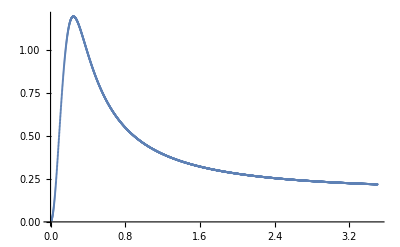

```mathematica
ListPlot[listV2, PlotRange->Full]
```

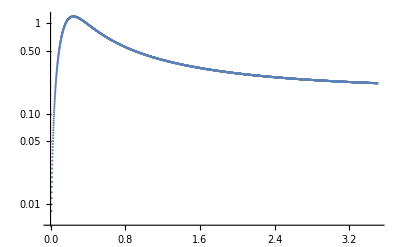

```mathematica
ListLogPlot[listV2, PlotRange->Full]
```